```mathematica
Quit
```

## Loading things

### Matrix

```mathematica
firstTotal=({{-(u[z] w[z])/(2 z), 0, 0, 0, 0, 0, 0, 0}, {0, -(u[z] w[z])/(2 z), 0, 0, 0, 0, 0, 0}, {0, 0, w[z]/(2 z^3), 0, -(c[z] w[z])/(2 z^3), 0, 0, 0}, {0, 0, 0, w[z]/(2 z^3), 0, -(c[z] w[z])/(2 z^3), 0, 0}, {0, 0, -(c[z] w[z])/(2 z^3), 0, (u[z]-c[z]^2 w[z]^2)/(2 z^3 w[z])+(-u[z]+c[z]^2 w[z]^2)/(z^3 w[z]), 0, 0, 0}, {0, 0, 0, -(c[z] w[z])/(2 z^3), 0, (u[z]-c[z]^2 w[z]^2)/(2 z^3 w[z])+(-u[z]+c[z]^2 w[z]^2)/(z^3 w[z]), 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}});
```

```mathematica
secondBulk=({{-(ⅈ (ω+k c[z]) w[z])/(2 z), -1/6 ⅈ γ (k AV[z]+ω P[z]), -(w[z] (AV'[z]-c[z] P'[z]))/(2 z), (B w[z])/(2 z vv[z]^2), (c[z] w[z]^2 AV'[z]+u[z] P'[z]-c[z]^2 w[z]^2 P'[z])/(2 z w[z]), -(B c[z] w[z])/(2 z vv[z]^2), 0, -(B u[z] w[z])/(2 z vv[z]^2)}, {1/6 ⅈ γ (k AV[z]+ω P[z]), -(ⅈ (ω+k c[z]) w[z])/(2 z), -(B w[z])/(2 z vv[z]^2), -(w[z] (AV'[z]-c[z] P'[z]))/(2 z), (B c[z] w[z])/(2 z vv[z]^2), (c[z] w[z]^2 AV'[z]+u[z] P'[z]-c[z]^2 w[z]^2 P'[z])/(2 z w[z]), (B u[z] w[z])/(2 z vv[z]^2), 0}, {0, 0, (z w[z] vv'[z]+vv[z] (-3 w[z]+z w'[z]))/(z^4 vv[z]), 0, -(z vv[z] w[z] c'[z]+2 c[z] (z w[z] vv'[z]+vv[z] (-3 w[z]+z w'[z])))/(2 z^4 vv[z]), 0, (ⅈ (ω+k c[z]) w[z])/(2 z^3), 0}, {0, 0, 0, (z w[z] vv'[z]+vv[z] (-3 w[z]+z w'[z]))/(z^4 vv[z]), 0, -(z vv[z] w[z] c'[z]+2 c[z] (z w[z] vv'[z]+vv[z] (-3 w[z]+z w'[z])))/(2 z^4 vv[z]), 0, (ⅈ (ω+k c[z]) w[z])/(2 z^3)}, {0, 0, (-2 z c[z] w[z]^2 vv'[z]+vv[z] (-ⅈ k z-z w[z]^2 c'[z]+2 c[z] w[z] (3 w[z]-z w'[z])))/(2 z^4 vv[z] w[z]), 0, (-2 z (u[z]-c[z]^2 w[z]^2) vv'[z]+vv[z] (-ⅈ z ω+6 u[z]+2 z c[z] w[z]^2 c'[z]-z u'[z]+2 c[z]^2 w[z] (-3 w[z]+z w'[z])))/(2 z^4 vv[z] w[z]), 0, -(ⅈ (-k u[z]+c[z] (ω+k c[z]) w[z]^2))/(2 z^3 w[z]), 0}, {0, 0, 0, (-2 z c[z] w[z]^2 vv'[z]+vv[z] (-ⅈ k z-z w[z]^2 c'[z]+2 c[z] w[z] (3 w[z]-z w'[z])))/(2 z^4 vv[z] w[z]), 0, (-2 z (u[z]-c[z]^2 w[z]^2) vv'[z]+vv[z] (-ⅈ z ω+6 u[z]+2 z c[z] w[z]^2 c'[z]-z u'[z]+2 c[z]^2 w[z] (-3 w[z]+z w'[z])))/(2 z^4 vv[z] w[z]), 0, -(ⅈ (-k u[z]+c[z] (ω+k c[z]) w[z]^2))/(2 z^3 w[z])}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}});
```

```mathematica
secondCounter=({{-(Log[z] (-k^2 u[z]+(ω+k c[z])^2 w[z]^2))/(2 √u[z] w[z]), 0, 0, -(ⅈ B (ω+k c[z]) Log[z] w[z])/(2 √u[z] vv[z]^2), 0, -(ⅈ B Log[z] (k u[z]-c[z] (ω+k c[z]) w[z]^2))/(2 √u[z] vv[z]^2 w[z]), 0, 0}, {0, -(Log[z] (-k^2 u[z]+(ω+k c[z])^2 w[z]^2))/(2 √u[z] w[z]), (ⅈ B (ω+k c[z]) Log[z] w[z])/(2 √u[z] vv[z]^2), 0, -(ⅈ B Log[z] (-k u[z]+c[z] (ω+k c[z]) w[z]^2))/(2 √u[z] vv[z]^2 w[z]), 0, 0, 0}, {0, -(ⅈ B (ω+k c[z]) Log[z] w[z])/(2 √u[z] vv[z]^2), (-2 k^2 z^4 (ω+k c[z])^2 Log[z] vv[z]^4 w[z]^2+u[z] (-4 B^2 z^4 Log[z] w[z]^4+vv[z]^4 (2 k^4 z^4 Log[z]+4 k^2 z^2 w[z]^2+48 w[z]^4)))/(16 z^4 u[z]^(3/2) vv[z]^4 w[z]^3), 0, (-2 k z^4 ω (ω+k c[z])^2 Log[z] vv[z]^4 w[z]^2+u[z] (4 B^2 z^4 c[z] Log[z] w[z]^4+vv[z]^4 (2 k^3 z^4 ω Log[z]+4 k z^2 ω w[z]^2-48 c[z] w[z]^4)))/(16 z^4 u[z]^(3/2) vv[z]^4 w[z]^3), 0, 0, 0}, {(ⅈ B (ω+k c[z]) Log[z] w[z])/(2 √u[z] vv[z]^2), 0, 0, (-2 k^2 z^4 (ω+k c[z])^2 Log[z] vv[z]^4 w[z]^2+u[z] (-4 B^2 z^4 Log[z] w[z]^4+vv[z]^4 (2 k^4 z^4 Log[z]+4 k^2 z^2 w[z]^2+48 w[z]^4)))/(16 z^4 u[z]^(3/2) vv[z]^4 w[z]^3), 0, (-2 k z^4 ω (ω+k c[z])^2 Log[z] vv[z]^4 w[z]^2+u[z] (4 B^2 z^4 c[z] Log[z] w[z]^4+vv[z]^4 (2 k^3 z^4 ω Log[z]+4 k z^2 ω w[z]^2-48 c[z] w[z]^4)))/(16 z^4 u[z]^(3/2) vv[z]^4 w[z]^3), 0, 0}, {0, -(ⅈ B Log[z] (k u[z]-c[z] (ω+k c[z]) w[z]^2))/(2 √u[z] vv[z]^2 w[z]), (-2 k z^4 ω (ω+k c[z])^2 Log[z] vv[z]^4 w[z]^2+u[z] (4 B^2 z^4 c[z] Log[z] w[z]^4+vv[z]^4 (2 k^3 z^4 ω Log[z]+4 k z^2 ω w[z]^2-48 c[z] w[z]^4)))/(16 z^4 u[z]^(3/2) vv[z]^4 w[z]^3), 0, (-2 z^4 ω^2 (ω+k c[z])^2 Log[z] vv[z]^4 w[z]^2-2 u[z]^2 (-2 B^2 z^4 Log[z]+24 vv[z]^4) w[z]^2+u[z] (-4 B^2 z^4 c[z]^2 Log[z] w[z]^4+vv[z]^4 (2 k^2 z^4 ω^2 Log[z]+4 z^2 ω^2 w[z]^2+48 c[z]^2 w[z]^4)))/(16 z^4 u[z]^(3/2) vv[z]^4 w[z]^3), 0, 0, 0}, {-(ⅈ B Log[z] (-k u[z]+c[z] (ω+k c[z]) w[z]^2))/(2 √u[z] vv[z]^2 w[z]), 0, 0, (-2 k z^4 ω (ω+k c[z])^2 Log[z] vv[z]^4 w[z]^2+u[z] (4 B^2 z^4 c[z] Log[z] w[z]^4+vv[z]^4 (2 k^3 z^4 ω Log[z]+4 k z^2 ω w[z]^2-48 c[z] w[z]^4)))/(16 z^4 u[z]^(3/2) vv[z]^4 w[z]^3), 0, (-2 z^4 ω^2 (ω+k c[z])^2 Log[z] vv[z]^4 w[z]^2-2 u[z]^2 (-2 B^2 z^4 Log[z]+24 vv[z]^4) w[z]^2+u[z] (-4 B^2 z^4 c[z]^2 Log[z] w[z]^4+vv[z]^4 (2 k^2 z^4 ω^2 Log[z]+4 z^2 ω^2 w[z]^2+48 c[z]^2 w[z]^4)))/(16 z^4 u[z]^(3/2) vv[z]^4 w[z]^3), 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}});
```

### Hard coded equations

```mathematica
vectorAFinal={B hV2[z] w[z]^2+2 ⅈ z ω w[z]^2 a1'[z]+2 ⅈ k z c[z] w[z]^2 a1'[z]-u[z] w[z]^2 a1'[z]-ⅈ k z^2 γ a2[z] w[z] AV'[z]+B z^2 γ h13[z] w[z] AV'[z]-z c[z] vv[z]^2 w[z]^2 AV'[z] h13'[z]+B z c[z] w[z]^2 h23'[z]+z vv[z]^2 w[z]^2 AV'[z] hV1'[z]-B z w[z]^2 hV2'[z]-ⅈ z ω h13[z] vv[z]^2 P'[z]-ⅈ k z hV1[z] vv[z]^2 P'[z]-ⅈ z^2 γ ω a2[z] w[z] P'[z]-B z^2 γ hV1[z] w[z] P'[z]-z u[z] vv[z]^2 h13'[z] P'[z]+z c[z]^2 vv[z]^2 w[z]^2 h13'[z] P'[z]-z c[z] vv[z]^2 w[z]^2 hV1'[z] P'[z]+z w[z]^2 a1'[z] u'[z]-B z hV2[z] w[z] w'[z]+z u[z] w[z] a1'[z] w'[z]+a1[z] (-k^2 z-ⅈ w[z]^2 (ω+k c[z]-k z c'[z])+ⅈ z (ω+k c[z]) w[z] w'[z])+B h23[z] (z (ⅈ k+w[z]^2 c'[z])+c[z] w[z] (-w[z]+z w'[z]))+z u[z] w[z]^2 a1''[z],-B hV1[z] w[z]^2+2 ⅈ z ω w[z]^2 a2'[z]+2 ⅈ k z c[z] w[z]^2 a2'[z]-u[z] w[z]^2 a2'[z]+ⅈ k z^2 γ a1[z] w[z] AV'[z]+B z^2 γ h23[z] w[z] AV'[z]-B z c[z] w[z]^2 h13'[z]-z c[z] vv[z]^2 w[z]^2 AV'[z] h23'[z]+B z w[z]^2 hV1'[z]+z vv[z]^2 w[z]^2 AV'[z] hV2'[z]-ⅈ z ω h23[z] vv[z]^2 P'[z]-ⅈ k z hV2[z] vv[z]^2 P'[z]+ⅈ z^2 γ ω a1[z] w[z] P'[z]-B z^2 γ hV2[z] w[z] P'[z]-z u[z] vv[z]^2 h23'[z] P'[z]+z c[z]^2 vv[z]^2 w[z]^2 h23'[z] P'[z]-z c[z] vv[z]^2 w[z]^2 hV2'[z] P'[z]+z w[z]^2 a2'[z] u'[z]+B z hV1[z] w[z] w'[z]+z u[z] w[z] a2'[z] w'[z]+a2[z] (-k^2 z-ⅈ w[z]^2 (ω+k c[z]-k z c'[z])+ⅈ z (ω+k c[z]) w[z] w'[z])+B h13[z] (-ⅈ k z-z w[z]^2 c'[z]+c[z] w[z] (w[z]-z w'[z]))+z u[z] w[z]^2 a2''[z],ⅈ B z^3 ω a2[z] w[z]^2+B^2 z^3 hV1[z] w[z]^2+z^3 vv[z]^2 w[z]^2 (-ⅈ a1[z] (ω+k c[z])-B c[z] h23[z]+B hV2[z]-u[z] a1'[z]) AV'[z]-4 ⅈ z vv[z]^3 w[z]^2 (c[z] (ω h13[z]+k hV1[z])-ⅈ u[z] hV1'[z]) vv'[z]+vv[z]^4 (ω h13[z] (k z+ⅈ c[z] w[z] (3 w[z]+z w'[z]))+k hV1[z] (k z+ⅈ c[z] w[z] (3 w[z]+z w'[z]))+w[z] (z c[z]^2 w[z]^3 c'[z] h13'[z]-ⅈ z ω w[z] hV1'[z]+z c[z] (-w[z]^3 c'[z] hV1'[z]-ⅈ w[z] (2 k hV1'[z]+h13'[z] (ω-ⅈ u'[z]))+2 u[z] h13'[z] w'[z])+u[z] (-z hV1'[z] w'[z]+w[z] (z c'[z] h13'[z]+3 hV1'[z]-z hV1''[z])))),-ⅈ B z^3 ω a1[z] w[z]^2+B^2 z^3 hV2[z] w[z]^2+z^3 vv[z]^2 w[z]^2 (-ⅈ a2[z] (ω+k c[z])+B c[z] h13[z]-B hV1[z]-u[z] a2'[z]) AV'[z]-4 ⅈ z vv[z]^3 w[z]^2 (c[z] (ω h23[z]+k hV2[z])-ⅈ u[z] hV2'[z]) vv'[z]+vv[z]^4 (ω h23[z] (k z+ⅈ c[z] w[z] (3 w[z]+z w'[z]))+k hV2[z] (k z+ⅈ c[z] w[z] (3 w[z]+z w'[z]))+w[z] (z c[z]^2 w[z]^3 c'[z] h23'[z]-ⅈ z ω w[z] hV2'[z]+z c[z] (-w[z]^3 c'[z] hV2'[z]-ⅈ w[z] (2 k hV2'[z]+h23'[z] (ω-ⅈ u'[z]))+2 u[z] h23'[z] w'[z])+u[z] (-z hV2'[z] w'[z]+w[z] (z c'[z] h23'[z]+3 hV2'[z]-z hV2''[z])))),-ⅈ B k z^3 a2[z] w[z]+z vv[z]^4 w[z]^3 c'[z] (c[z] h13'[z]-hV1'[z])+z vv[z]^4 (ⅈ ω h13[z]+ⅈ k hV1[z]+u[z] h13'[z]) w'[z]+w[z] (h13[z] (B^2 z^3+3 ⅈ ω vv[z]^4-4 ⅈ z ω vv[z]^3 vv'[z])+vv[z]^2 (z^3 (-ⅈ a1[z] (ω+k c[z])-B c[z] h23[z]+B hV2[z]-u[z] a1'[z]) P'[z]+4 z vv[z] (-ⅈ k hV1[z]-u[z] h13'[z]) vv'[z]-ⅈ vv[z]^2 (-3 k hV1[z]+h13'[z] (2 z ω+k z c[z]+3 ⅈ u[z]-ⅈ z u'[z])+z (k hV1'[z]-ⅈ u[z] h13''[z])))),ⅈ B k z^3 a1[z] w[z]+z vv[z]^4 w[z]^3 c'[z] (c[z] h23'[z]-hV2'[z])+z vv[z]^4 (ⅈ ω h23[z]+ⅈ k hV2[z]+u[z] h23'[z]) w'[z]+w[z] (h23[z] (B^2 z^3+3 ⅈ ω vv[z]^4-4 ⅈ z ω vv[z]^3 vv'[z])+vv[z]^2 (z^3 (-ⅈ a2[z] (ω+k c[z])+B c[z] h13[z]-B hV1[z]-u[z] a2'[z]) P'[z]+4 z vv[z] (-ⅈ k hV2[z]-u[z] h23'[z]) vv'[z]-ⅈ vv[z]^2 (-3 k hV2[z]+h23'[z] (2 z ω+k z c[z]+3 ⅈ u[z]-ⅈ z u'[z])+z (k hV2'[z]-ⅈ u[z] h23''[z])))),-ⅈ B z^2 a2[z] (ω+k c[z]) w[z]^2+B z^2 w[z]^2 (B c[z] h13[z]-B hV1[z]-u[z] a2'[z])-vv[z]^4 (k ω h13[z]+k^2 hV1[z]-ⅈ (k u[z] h13'[z]-(ω+k c[z]) w[z]^2 (c[z] h13'[z]-hV1'[z])))+z^2 vv[z]^2 (ⅈ a1[z] (k u[z] P'[z]+(ω+k c[z]) w[z]^2 (AV'[z]-c[z] P'[z]))+B (-hV2[z] w[z]^2 AV'[z]+h23[z] u[z] P'[z]-c[z]^2 h23[z] w[z]^2 P'[z]+c[z] w[z]^2 (h23[z] AV'[z]+hV2[z] P'[z]))),ⅈ B z^2 a1[z] (ω+k c[z]) w[z]^2+B z^2 w[z]^2 (B c[z] h23[z]-B hV2[z]+u[z] a1'[z])-vv[z]^4 (k ω h23[z]+k^2 hV2[z]-ⅈ (k u[z] h23'[z]-(ω+k c[z]) w[z]^2 (c[z] h23'[z]-hV2'[z])))+z^2 vv[z]^2 (ⅈ a2[z] (k u[z] P'[z]+(ω+k c[z]) w[z]^2 (AV'[z]-c[z] P'[z]))+B (hV1[z] w[z]^2 AV'[z]-h13[z] u[z] P'[z]+c[z]^2 h13[z] w[z]^2 P'[z]-c[z] w[z]^2 (h13[z] AV'[z]+hV1[z] P'[z])))};
```

### Get four term fluctuation expansion here

```mathematica
(* Import the horizon expansion of the background here*)

SetDirectory[NotebookDirectory[]];
Quiet[Get["horExpBack6.m"]];
```

Saved with name “horSeries”, “flucHorSeries”

```mathematica
SetDirectory[NotebookDirectory[]];
Quiet[Get["flucExpSixEqnSystJWtype.m"]];

flucHorSeries=flucHorSeries;
```

```mathematica
subFluc0={c1[0]->(v[0]^4 (av[0] v[0]^2 (ⅈ k c13[0]-cv1[0] w[0]^2)+B (-ⅈ k c23[0]+cv2[0] w[0]^2)))/((B^2+av[0]^2 v[0]^4) w[0]^2),c2[0]->(ⅈ v[0]^4 (B (k c13[0]+ⅈ cv1[0] w[0]^2)+av[0] v[0]^2 (k c23[0]+ⅈ cv2[0] w[0]^2)))/((B^2+av[0]^2 v[0]^4) w[0]^2)};
```

```mathematica
Coefficient[hV1[z]/.flucHorSeries,c1[2]]//Simplify
```

0

### Psub and ruleBDR

```mathematica
functions={{u[z],w[z],vv[z],c[z]},{AV[z],P[z]}}//Flatten;
```

```mathematica
psub={c->((1-#1) #1^4 c[#1]&),
u->(1+1/6 B^2 #1^4 Log[#1]+#1^4 u[#1]&),
vv->(1-1/24 B^2 #1^4 Log[#1]+#1^4 vv[#1]&),w->(1+1/12 B^2 #1^4 Log[#1]+#1^4 w[#1]&),
AV->((1-#1) AV[#1]&),P->(#1^2 P[#1]&)};
```

```mathematica
ruleBDR={u->Function[z,1+z^4 u4+1/6 z^4 Log[z] B^2(*+O[z]^6*)],vv->Function[z,1+1/2 z^4 (-w4)+1/24 z^4 Log[z] (-B^2)(*+O[z]^6*)],w->Function[z,1+z^4 w4+1/12 z^4 Log[z] B^2(*+O[z]^6*)],c->Function[z,z^4 (c4+1/12 z^4 Log[z] (-B^2))(*+O[z]^6*)],P->Function[z,z^2 (p1/2+1/8 (γ B ρ) z^2)(*+O[z]^6*)],AV->Function[z,μ-(ρ z^2)/2-1/8 (γ B p1) z^4(*+O[z]^6*)]};
```

## Background

### Import ***

```mathematica
SetDirectory[NotebookDirectory[]<>"backgrounds"];
backData=Get["back090119γSUSYμT10B0p0725"];
```

```mathematica
γSub=backData⟦1,1⟧;
mutilde=backData⟦1,2⟧
bSub=backData⟦1,3⟧;
bSub//N

background=backData⟦2⟧;
```

10

0.0725

```mathematica
prec1=60;
gSize=1/6 Length[background];
zgrid=SetPrecision[Table[1/2 (1-Cos[(n π)/(gSize-1)]),{n,0,gSize-1}],prec1];
{uSub,wSub,vSub,cSub,avSub,pSub}=Interpolation[{zgrid,background⟦gSize #+1;;gSize(#+1)⟧}//Transpose]&/@Range[0,5];

backSub=SetPrecision[{u->uSub,w->wSub,vv->vSub,c->cSub,AV->avSub, P->pSub},prec1];
```

### g20 ***

```mathematica
SetDirectory[NotebookDirectory[]];
Get["g20"];
```

```mathematica
mutilde=10;
bSub=10^-5;
```

```mathematica
background=newton[initguess[1/mutilde],abc/.{b0->bSub,temp->1/mutilde},abc2/.{b0->bSub,temp->1/mutilde}]
```

start norm: 8.180×10^-4

iteration: 1 norm: 1.390×10^-9		 T subt: 1.217  T solve: 0.0624001

iteration: 2 norm: 0.×10^-20		 T subt: 1.170  T solve: 0.0468001

overall time: 2.7456

{-1.94312266155280005253413814276465099908333858910630029842266,-1.94307880303752749211277839080204008988576098988028662774093,-1.94243046344296793426487091796488074424233230360533393233942,-1.93969757564479245537145872720956334204812430633231880821818,-1.93263944650020246127573828922814034761521642757394988313418,-1.918566769207539544638708871180739419193429535717883977362,-1.89472727203344453289094103460326237012757901062939146925239,-1.85872064229149752036094132067643383605779653417718188289417,-1.80889457959582818269592799744145879583741753758495427272058,-1.74467535172734924438746534308699836574547111018282880691502,-1.66679289963536313349879057121586522008597714889420282764425,-1.5773716535886980803099788791481203106914825826856367073202,-1.47987258425589957466661968603237418112364387930403747735536,-1.37888806940996843774962589138982930024102629002065732966211,-1.27980717075183997696872539598066051917715729962802072908975,-1.18838314893651322687028360697460154598911493132025212930404,-1.11024595063940763775486803136922532187973978596509339035903,-1.05040878910691443982611233617881945340810142665479840872669,-1.01281910531944698134066174696045831432765490847489757089175,-1.,3.9950483316590553043888412128033996750401339887272496372019×10^-12,3.9944635028802931624471446178224069797725632165942894057142×10^-12,3.985809828535092298952022602190448095628603944196301013395×10^-12,3.9492414965065872035839448806141156817785134269394123519796×10^-12,3.8545218596202233863483419516256971127597737701209511873233×10^-12,3.6657630088101348529171260259088150420147606869035033811441×10^-12,3.3490584770538429433208910053970474403471882106583007272465×10^-12,2.882308132294961055846525965577079276679566966546261760016×10^-12,2.2640264770310978313099694491643319749320657915277414218361×10^-12,1.5169119490187352387967406470273183957236356167648817521373×10^-12,6.8418263762316122478736827281223962050502421745275139185216×10^-13,-1.794821668523707335310016240632535358407186488828748185831×10^-13,-1.0184176402386262891752667326777064220129714175257288773326×10^-12,-1.784556551972934651369399684098692326727236138652930243132×10^-12,-2.4427503801167371142629253408014872700961562863733346365123×10^-12,-2.9729048904386974983216908892029253441792526874689766298717×10^-12,-3.3694273767875333617185381988268756201242427515307221548478×10^-12,-3.6382639645793417587240745676716600586332719834572039859729×10^-12,-3.791636202214155084131946110467480845104084113122583376024×10^-12,-3.8411767300167405415193160316825262242566673099703429276257×10^-12,-1.9975241658045985458705967265505286628780793722104246826685×10^-12,-1.997377939213206745499295897979273181486235247064756368343×10^-12,-1.9952104283302764763452874572648090333491397481723620401998×10^-12,-1.9859934507939204751912452918041528874981918653661544688144×10^-12,-1.9617937454524890058671867940018922507653460520080374948071×10^-12,-1.9125132539710330985927543659211063247392307266011569997023×10^-12,-1.8274400675902240950521791506152987859152411442379901657463×10^-12,-1.6978642883701729278528720898252003921161471418065772947371×10^-12,-1.5201259017225218074959338785434327281884083391739910835629×10^-12,-1.2977042398954782085868446497612270335520662224267498124297×10^-12,-1.0412262552534944104510949975070938118609430905236232082817×10^-12,-7.664271840686140090610333177664601860910008070605301316833×10^-13,-4.9107990850130126993696760373503878547490555670065180334465×10^-13,-2.320365836795559452801415250307386500378169925708203853117×10^-13,-3.04627608994782573362856063627950070829417486395420019949×10^-15,1.864902467137723575118399792453288897544487549082005734943×10^-13,3.3188521538168780604889265499948149643002577059692996857749×10^-13,4.3266371029011319937035889531210128262713401195815477014543×10^-13,4.9113717540779901090790102479926825317219808138672306636551×10^-13,5.102011133445241893914786444762554007122603040597024449521×10^-13,4.08384091892633592200185672912199732212540660543875547148611×10^-6,4.11162631802270876112815931811212062769732278067785379617774×10^-6,4.1934520089900122280520311422920585187108438753156203097881×10^-6,4.32471380878834012892714748245156248828437996849699881337496×10^-6,4.49776469114310030834160383573257480779576388233824512649131×10^-6,4.70216636300370440810363376391561766040288917135640470576386×10^-6,4.925353810832427802199668313625978478963895118211930102355×10^-6,5.15377587340253599112099825154615101060174515348325952343438×10^-6,5.37433531521940447130103098899618855480245224398873904077347×10^-6,5.57575846086406187071027333465729314158035133838437882557261×10^-6,5.74954442927049419328366822573509517703099547664373399369332×10^-6,5.89037034775418652350348021808655335440670705947667531040528×10^-6,5.99607482238737544238745761620217728079774493813638444069169×10^-6,6.06743951339491566478709556479845431990618355671797408019101×10^-6,6.10792387902667168469171035575492654591269620369054075922899×10^-6,6.1233647424037260722483600715093020101844706772087854438036×10^-6,6.12150855866077136020061011016484954181265023630837145734793×10^-6,6.11115594589517796134165596573899705344444639520814731785494×10^-6,6.1007471926640313873304013034029891110379381806778234715627×10^-6,6.09650758755706255713225017558426079554036954995218470496713×10^-6,1.68207252656906792316475261873187927851710365360651823884986,1.69354316499131291818985219009763765311356838941658609464886,1.72764219114360122905040766763273802646148104481729240058741,1.78343947248199315214451173586543015721762654759510778589795,1.85941300462417876969131194266291174502211865132678073777786,1.95349042766145863970699258317873133530602726615416621488281,2.06310555473481902341924227365468014848231259312226586013668,2.18526837092290595120412550282771264338403134914660048837207,2.31664659305470504474162999904378950761246070649195548588641,2.45365656570784324064173975756394913290485774056815518815034,2.59256101398662447431454732558937857106930399538150237638893,2.72957098663883935302353470441444545662554686414489439861657,2.86094920876887319385401501646208444334010663334979872579956,2.9831120249545210296922996545161240265062972577188992466399,3.09272715202502278663425490617807815390962400261142325839216,3.18680457505934495000073246635445404834329534266613360950014,3.26277810719881625318700365717302160281229200134009521073934,3.31857538853504512459744922342374999511467695540652551248403,3.35267441468594913729059262902790611423159931387020403650767,3.36414505310771902921344054192784761417616057452836710539242,-9.71145026012089092983967490726585782125984581490663269556727×10^-6,-9.71122446050555622105711615106237157828245225351500905892731×10^-6,-9.70788858853975573159619745300777397039254729322206484317317×10^-6,-9.69386853008579573172166037613350282568976011484480003028556×10^-6,-9.65796465158452327763423315865674554118089381513581385197277×10^-6,-9.58765398248750319327041663003452397906363827861694073006698×10^-6,-9.47221750201071514875099406803940204872286489275802988045464×10^-6,-9.30589215597529602973301607696567743300834371555657938527584×10^-6,-9.08980984127615104569074345870582411652667908185724816401003×10^-6,-8.83183425804791425115073839810332090490318757162229758885081×10^-6,-8.54449946026403665059789558609695538378524265422846844494999×10^-6,-8.24221439735328077829928415021501641648862626290938930598951×10^-6,-7.93897576154562081191853856260701811158649275819150694296898×10^-6,-7.64719531224993592199673660100690327824765542812698048368403×10^-6,-7.3775619956877047022096348273952528581556408235576080961854×10^-6,-7.13950774475980980938178493743722744922781176942204904188706×10^-6,-6.94178150196888213747393866420066966888508234299946918502966×10^-6,-6.79268187729194433133277076081915625441074544102874654622406×10^-6,-6.69961143515051094134080508087266745077471463823027772392676×10^-6,-6.66792629594914964769155762739915087732644129077052306083988×10^-6}

```mathematica
γSub=2/(√3);
μSub=mutilde;
bSub=bSub;
```

```mathematica
prec1=60;
gSize=1/6 Length[background];
zgrid=SetPrecision[Table[1/2 (1-Cos[(n π)/(gSize-1)]),{n,0,gSize-1}],prec1];
{uSub,wSub,vSub,cSub,avSub,pSub}=Interpolation[{zgrid,background⟦gSize #+1;;gSize(#+1)⟧}//Transpose]&/@Range[0,5];

backSub=SetPrecision[{u->uSub,w->wSub,vv->vSub,c->cSub,AV->avSub, P->pSub},prec1];
```

### Check

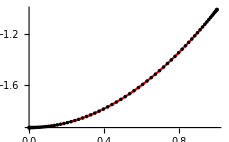
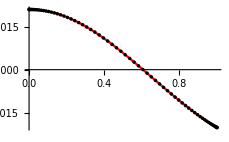
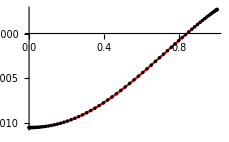
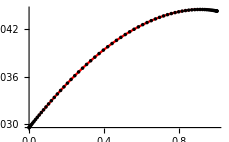
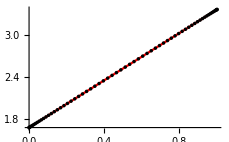
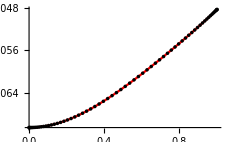

```mathematica
Table[ListPlot[{zgrid,background⟦gSize i+1;;gSize(i+1)⟧}//Transpose,PlotStyle->Black],{i,0,5}];
Plot[backSub⟦#,2⟧[z],{z,0,1},PlotStyle->Red]&/@Range[Length[backSub]];
Show[%⟦#⟧,%%⟦#⟧,ImageSize->230]&/@Range[6]
```

```mathematica
backSub//Precision
backData//Precision
background//Precision
```

60.

57.3307

57.3307

### RNS check (OK)

```mathematica
RNS={u->Function[z,1-z^4+1/3 z^4(z^2-1)μ^2],w->Function[z,1],vv->Function[z,1],c->Function[z,0],P->Function[z,0],AV->Function[z,μ z^2-μ],B->0};
```

```mathematica
ftaap=u'[z]/(4π)/.RNS/.z->1
μSub=Solve[mutilde==μ/ftaap,μ]//Flatten//Simplify
```

(-4+(2 μ^2)/3)/(4 π)

{μ→1/10 (3 π-√(600+9 π^2)),μ→1/10 (3 π+√(600+9 π^2))}

```mathematica
psubInv=Solve[{uT[z],wT[z],vT[z],cT[z],PT[z],AVT[z]}=={u[z],w[z],vv[z],c[z],P[z],AV[z]}/.psub,{u[z],w[z],vv[z],c[z],P[z],AV[z]}]/.{uT->u,wT->w,vT->vv,cT->c,PT->P,AVT->AV}//Simplify//Flatten
```

{u[z]→-(6+B^2 z^4 Log[z]-6 u[z])/(6 z^4),w[z]→-1/z^4-1/12 B^2 Log[z]+w[z]/z^4,vv[z]→-1/z^4+1/24 B^2 Log[z]+vv[z]/z^4,c[z]→-c[z]/((-1+z) z^4),P[z]→P[z]/z^2,AV[z]→-AV[z]/(-1+z)}

```mathematica
{u[z],w[z],vv[z],c[z],P[z],AV[z]}/.psub/.psubInv//Simplify
{u[z],w[z],vv[z],c[z],P[z],AV[z]}/.psubInv/.psub//Simplify
```

{u[z],w[z],vv[z],c[z],P[z],AV[z]}

{u[z],w[z],vv[z],c[z],P[z],AV[z]}

```mathematica
μSub⟦1⟧//N
```

μ→-1.68207

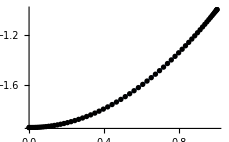
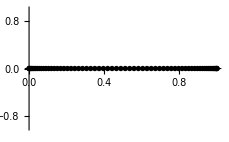
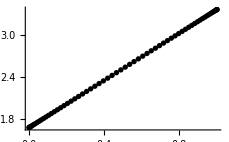
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListPlot[{zgrid,background⟦gSize i+1;;gSize(i+1)⟧}//Transpose,PlotStyle->Black],{i,0,5}];
Plot[#,{z,0,1}]&/@({u[z],w[z],vv[z],c[z],AV[z],P[z]}/.psubInv/.RNS/.μSub⟦1⟧//Simplify);
Show[%⟦#⟧,%%⟦#⟧,ImageSize->230]&/@Range[6]
```

```mathematica
Clear[backSub]
```

### Thermodynamics

```mathematica
taap=SetPrecision[1/(4π)Abs[u'[z]/.psub/.backSub/.B->bSub/.z->1],prec1]
entropy=SetPrecision[4π vv[z]^2 w[z]/.psub/.backSub/.B->bSub/.z->1,prec1]
n0=SetPrecision[-D[AV[z]/.psub/.backSub,{z,2}]/.z->0,prec1]
u4=background⟦1⟧;
w4=background⟦68+1⟧;
ϵ0=-3u4
p0=-u4+8w4
w0=ϵ0+p0
```

0.168210461888062175763090739549234723209341751093233143598789

12.5645079065133528533074054714285415393390247577444047977329

3.36615859835511715014603706291118925609913633084809482471445

5.830524758814834099272516265523144249581009312632917404708

1.9451878205702174665942556156845936910010245467104306066355

7.7757125793850515658667718812077379405820338593433480113435

```mathematica
bSub/taap^2
```

2.562311937276675198302371682713841317958367931892172679068

## Green function (ω ≠ 0, k=0)

### Hyperparameter

```mathematica
zBdr=10^-10;
zHor=1-10^-10;

wp=prec1-2; 
pg=21; 
ag=10^2;
```

### Green function

```mathematica
vectorEQN=SetPrecision[vectorAFinal/.psub/.backSub/.{B->bSub,γ->γSub}//Simplify,prec1];

uNot=-SetPrecision[u'[z]/.psub/.backSub/.B->bSub/.z->zHor,prec1];
vNot=SetPrecision[vv[z]/.psub/.backSub/.B->bSub/.z->zHor,prec1];
wNot=SetPrecision[w[z]/.psub/.backSub/.B->bSub/.z->zHor,prec1];
cNot=-SetPrecision[c'[z]/.psub/.backSub/.B->bSub/.z->zHor,prec1];
avNot=-SetPrecision[AV'[z]/.psub/.backSub/.B->bSub/.z->zHor,prec1];
pNot=SetPrecision[P[z]/.psub/.backSub/.B->bSub/.z->zHor,prec1];

ruleUVWCAVP1=SetPrecision[{u[0]->uNot,v[0]->vNot,w[0]->wNot,c[0]->cNot,av[0]->avNot,p[0]->pNot},prec1];

beingSpecific=SetPrecision[{{c1[0]->z1,cv1[0]-> zV1, c13[0]->z13},{c2[0]->z2,cv2[0]-> zV2, c23[0]->z23},{B->bSub,γ->γSub}}//Flatten,prec1];

positionType=SetPrecision[{a1[z],a2[z],hV1[z],hV2[z],h13[z],h23[z]}/.flucHorSeries/.subFluc0/.beingSpecific/.ruleUVWCAVP1/.z->zHor,prec1];

velocityType=SetPrecision[D[{a1[z],a2[z],hV1[z],hV2[z],h13[z],h23[z]}/.flucHorSeries/.subFluc0/.beingSpecific/.ruleUVWCAVP1,z]/.z->zHor,prec1];
```

```mathematica
solSix[omega_?NumericQ,momentum_?NumericQ, hv1Zero_?NumericQ,hv2Zero_?NumericQ,h13Zero_?NumericQ,h23Zero_?NumericQ]:=Block[{ω=omega,k=momentum,zV1=hv1Zero,zV2=hv2Zero, z13=h13Zero,z23=h23Zero},NDSolve[{0== vectorEQN⟦1⟧,0== vectorEQN⟦2⟧, 0==vectorEQN⟦3⟧,0== vectorEQN⟦4⟧,0== vectorEQN⟦5⟧, 0==vectorEQN⟦6⟧,a1[zHor]==positionType⟦1⟧,a2[zHor]== positionType⟦2⟧, hV1[zHor]== positionType⟦3⟧,hV2[zHor]==positionType⟦4⟧,h13[zHor]==positionType⟦5⟧, h23[zHor]==positionType⟦6⟧,a1'[zHor]==velocityType⟦1⟧,a2'[zHor]== velocityType⟦2⟧,hV1'[zHor]==velocityType⟦3⟧,hV2'[zHor]==velocityType⟦4⟧,h13'[zHor]== velocityType⟦5⟧,h23'[zHor]==velocityType⟦6⟧},{a1[z],a2[z],hV1[z],hV2[z],h13[z],h23[z]},{z,zBdr,zHor},MaxSteps->10^6,WorkingPrecision->wp,PrecisionGoal->pg,AccuracyGoal->ag]]

pureGauge1[ω_,k_,B_]={B,0,0,ⅈ ω,0,-ⅈ k}; 
pureGauge2[ω_,k_,B_]={0,B,-ⅈ ω,0,ⅈ k,0};

hIJ[ω_,k_]:=SetPrecision[Transpose[({{pureGauge1[ω,k,bSub]}, {pureGauge2[ω,k,bSub]}, {solSix[ω,k,-1,1,1,1]⟦1,;;,2⟧}, {solSix[ω,k,1,-1,1,1]⟦1,;;,2⟧}, {solSix[ω,k,1,1,-1,1]⟦1,;;,2⟧}, {solSix[ω,k,1,1,1,-1]⟦1,;;,2⟧}})] ,prec1]

hIJ0[ω_,k_]:=SetPrecision[hIJ[ω,k]/.z->zBdr,prec1]
hIJ0I[ω_,k_]:=SetPrecision[Inverse[hIJ0[ω,k]],prec1]
fQ[ω_,k_]:=SetPrecision[hIJ[ω,k].hIJ0I[ω,k],prec1]
fQp[ω_,k_]:=SetPrecision[D[fQ[ω,k],z] ,prec1]

first[ω_,k_]=SetPrecision[Table[firstTotal⟦i,j⟧,{i,6},{j,6}]/.{B->bSub,γ->γSub}//Simplify,prec1];
second[ω_,k_]=SetPrecision[Table[(secondBulk+secondCounter)⟦i,j⟧,{i,6},{j,6}]/.{B->bSub,γ->γSub}//Simplify,prec1];

green[ω_,k_]:=SetPrecision[-2(first[ω,k].fQp[ω,k]+second[ω,k]),prec1]
```

```mathematica
green[1/100,0]/.psub/.backSub/.{B->bSub,γ->γSub}/.z->zBdr
```

{{0.164581871023718034265469869455970416+0.000102554567179805830288433252575292 ⅈ,-0.000059351105326197531608081255103553+0.516764940011727837517763145101084361 ⅈ,0.41036426960681415506218983619408093+0.00043029551361493210415858909950076 ⅈ,-0.000743520612053592269591141081170149+1.19321856492195574842465655355578552 ⅈ,-0.005795996302812822878392366582793325+4.26954395317474682201387346621×10^-7 ⅈ,-0.00001058065810478027780690804715204-0.018182961240079020338925297847166071 ⅈ},{0.000059351105326197531608081255103553-0.516764940011727837517763145101084361 ⅈ,0.164581871023718034265469869455970416+0.000102554567179805830288433252575292 ⅈ,0.000743520612053592269591141081170149-1.19321856492195574842465655355578552 ⅈ,0.41036426960681415506218983619408093+0.00043029551361493210415858909950076 ⅈ,0.00001058065810478027780690804715204+0.018182961240079020338925297847166071 ⅈ,-0.005795996302812822878392366582793325+4.26954395317474682201387346621×10^-7 ⅈ},{0.38038723151931352+0.00043029551194423 ⅈ,-0.0007435206087575+1.1932185648799357 ⅈ,2.859375241565563+0.0053905244134919 ⅈ,-0.0031196424615957+2.757807428515023 ⅈ,-0.0133905631952562+0.00007670977086439 ⅈ,-3.0954413214×10^-6-0.0420209731895686 ⅈ},{0.0007435206087575-1.1932185648799357 ⅈ,0.38038723151931352+0.00043029551194423 ⅈ,0.0031196424615957-2.757807428515023 ⅈ,2.859375241565563+0.0053905244134919 ⅈ,3.0954413214×10^-6+0.0420209731895686 ⅈ,-0.0133905631952562+0.00007670977086439 ⅈ},{-0.0057959963765416+4.269575896×10^-7 ⅈ,-0.0000105806587933-0.0181829614733066 ⅈ,-0.013390564882727+0.0000767097762513 ⅈ,-3.095442525×10^-6-0.042020973729926 ⅈ,-1.98018357494652+0.0099962902908472 ⅈ,8.189782499×10^-7+0.0006399271559696 ⅈ},{0.0000105806587933+0.0181829614733066 ⅈ,-0.0057959963765416+4.269575896×10^-7 ⅈ,3.095442525×10^-6+0.042020973729926 ⅈ,-0.013390564882727+0.0000767097762513 ⅈ,-8.189782499×10^-7-0.0006399271559696 ⅈ,-1.98018357494652+0.0099962902908472 ⅈ}}

```mathematica
green[7,0]/.psub/.backSub/.{B->bSub,γ->γSub}/.z->zBdr
```

{{-89.629247386053231330723606813720567701+76.950725682900622121686566874521690392 ⅈ,-0.001739437976420398949639356618287055-0.015729710289921321321445730887619595 ⅈ,-3.33634446033478685205527936800154532049+0.0000180156076129255605498361935465445 ⅈ,-0.79698965885861358626032515691468822021-0.92830291935555132449678021342782016547 ⅈ,0.095001719955862812383380008100387478+0.00012654054969731087460819083938715 ⅈ,0.000185610989332155378066811104397119-0.000065248683230134878254955322624228 ⅈ},{0.001739437976420398949639356618287055+0.015729710289921321321445730887619595 ⅈ,-89.629247386053231330723606813720567701+76.950725682900622121686566874521690392 ⅈ,0.79698965885861358626032515691468822021+0.92830291935555132449678021342782016547 ⅈ,-3.33634446033478685205527936800154532049+0.0000180156076129255605498361935465445 ⅈ,-0.000185610989332155378066811104397119+0.000065248683230134878254955322624228 ⅈ,0.095001719955862812383380008100387478+0.00012654054969731087460819083938715 ⅈ},{-3.366321493316088+0.000018017510433 ⅈ,-0.7969896588947541-0.9283029193723549 ⅈ,-5.801073919764612888+0.008254535752838525 ⅈ,-1.8660992949×10^-7-0.0348654726093452 ⅈ,0.118435229929396-1.922327668×10^-6 ⅈ,-1.310573255×10^-6+0.0009839465917345 ⅈ},{0.7969896588947541+0.9283029193723549 ⅈ,-3.366321493316088+0.000018017510433 ⅈ,1.8660992949×10^-7+0.0348654726093452 ⅈ,-5.801073919764612888+0.008254535752838525 ⅈ,1.310573255×10^-6-0.0009839465917345 ⅈ,0.118435229929396-1.922327668×10^-6 ⅈ},{0.095001698412622+0.000126572735965 ⅈ,0.0001856109025208-0.0000652486636583 ⅈ,0.11843523000901461-1.922398633251×10^-6 ⅈ,-1.31093190821×10^-6+0.000983946162130728 ⅈ,-1102.564021272696065+942.8958694819995577 ⅈ,-0.0000234726139701-5.8896671298×10^-6 ⅈ},{-0.0001856109025208+0.0000652486636583 ⅈ,0.095001698412622+0.000126572735965 ⅈ,1.31093190821×10^-6-0.000983946162130728 ⅈ,0.11843523000901461-1.922398633251×10^-6 ⅈ,0.0000234726139701+5.8896671298×10^-6 ⅈ,-1102.564021272696065+942.8958694819995577 ⅈ}}

### ω grid

```mathematica
prec1=60;
ωgSize=50;
ωAxis=SetPrecision[Table[L+ (1-Cos[(n π)/(2ωgSize-1)])(U-L),{n,0,2ωgSize-1}]⟦;;ωgSize⟧/.{L->10^-2,U->16π taap},prec1];
```

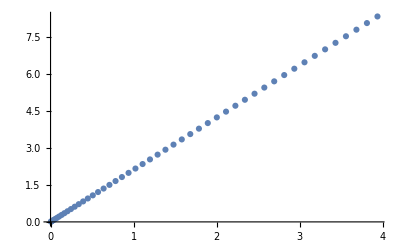

```mathematica
{ωAxis/(4π taap),ωAxis}//Transpose//ListPlot
```

```mathematica
ωAxis⟦1⟧-ωAxis⟦2⟧//Precision
```

59.2438

```mathematica
ωAxis⟦-1⟧/(4π taap)
```

3.936611203802241525214612269178386035322793502094451842486

### Computation

```mathematica
"corrγSUSYμT"<>ToString[mutilde]<>"B"<>ToString[10^6 bSub]<>"d10p6"
```

corrγSUSYμT10B72500d10p6

```mathematica
"corrγSUSYμT"<>ToString[100mutilde]<>"d100B"<>ToString[10^6 bSub]<>"d10p6"
```

corrγSUSYμT1000d100B72500d10p6

```mathematica
Beep[]
```

```mathematica
all=ParallelMap[SetPrecision[green[#,0]/.psub/.backSub/.{B->bSub,γ->γSub}/.z->zBdr,prec1]&,ωAxis]
```

NDSolve::mxst: Maximum number of 1000000 steps reached at the point z == 0.9992420840148881742314334778475444876636327176737202482932.

NDSolve::mxst: Maximum number of 1000000 steps reached at the point z == 0.9983581778684684076057549243473130922405439283197168766419.

```mathematica
all//Dimensions
```

{20,6,6}

```mathematica
toSave={{2/(√3),mutilde,bSub,taap,entropy,n0,p0,kSub},all};
```

```mathematica
SetDirectory[NotebookDirectory[]<>"f_data"];
Save["corrγSUSYμT"<>ToString[100mutilde]<>"d100B"<>ToString[10^6 bSub]<>"d10p6",toSave]
```

```mathematica
kSub=10^-8;
```

```mathematica
allk=Table[SetPrecision[green[ωAxis⟦i⟧,kSub]/.psub/.backSub/.{B->bSub,γ->γSub}/.z->zBdr,prec1],{i,Length[ωAxis]}]
```

```mathematica
toSavek={{2/(√3),mutilde,bSub,taap,entropy,n0,p0,kSub},allk};
```

```mathematica
SetDirectory[NotebookDirectory[]<>"Chiral_conductivity"];
Save["corChiralγSUSYμT"<>ToString[mutilde]<>"B"<>ToString[10^6 bSub]<>"d10p6",toSavek]
```

### ω grid (Long range)

```mathematica
prec1=60;
ωgSize=30;
ωAxis=SetPrecision[Table[L+ (1-Cos[(n π)/(2ωgSize-1)])(U-L),{n,0,2ωgSize-1}]⟦;;ωgSize⟧/.{L->10^-2,U->100 16π taap},prec1];
```

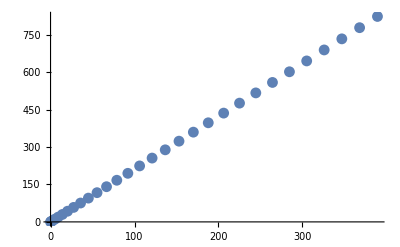

```mathematica
{ωAxis/(4π taap),ωAxis}//Transpose//ListPlot
```

```mathematica
ωAxis⟦1⟧-ωAxis⟦2⟧//Precision
```

59.9928

```mathematica
ωAxis⟦-1⟧
```

822.994735616218747267680925235321929796393727391558718093194

```mathematica
ωAxis⟦-1⟧/(4π taap)
```

389.35191736434771656089123755850089653437090169247464433006

### Computation (Long range)

```mathematica
all=Table[SetPrecision[green[ωAxis⟦i⟧,0]/.psub/.backSub/.{B->bSub,γ->γSub}/.z->zBdr,prec1],{i,Length[ωAxis]}]
```

No more memory available.
Mathematica kernel has shut down.
Try quitting other applications and then retry.

```mathematica
all//Dimensions
```

{50,6,6}

```mathematica
toSave={{2/(√3),mutilde,bSub,taap,entropy,n0,p0,kSub},all};
```

```mathematica
SetDirectory[NotebookDirectory[]<>"f_data"];
Save["LRcorrγSUSYμT"<>ToString[mutilde]<>"B"<>ToString[10^6 bSub]<>"d10p6",toSave]
```

```mathematica
"LRcorrγSUSYμT"<>ToString[mutilde]<>"B"<>ToString[10^6 bSub]<>"d10p6"
```

corrγSUSYμT1B821600d10p6

## Green function RNS (ω ≠ 0, k=0)

### Thermodynamics

```mathematica
taap=1/(4π)Abs[u'[z]/.RNS/.μSub⟦1⟧/.z->1]//Simplify
entropy=4π vv[z]^2 w[z]/.RNS/.z->1
n0=-D[AV[z]/.RNS,{z,2}]/.z->0
{u4,w4}=Coefficient[{u[z],w[z]}/.RNS,z^4]/.μSub⟦1⟧//Simplify;
ϵ0=-3u4
p0=-u4+8w4
w0=ϵ0+p0
```

1/100 (-3 π+√(600+9 π^2))

4 π

-2 μ

-3 (-1-1/300 (-3 π+√(600+9 π^2))^2)

1+1/300 (-3 π+√(600+9 π^2))^2

1+1/300 (-3 π+√(600+9 π^2))^2-3 (-1-1/300 (-3 π+√(600+9 π^2))^2)

```mathematica
bSub/taap^2
```

0

### Hyperparameter

```mathematica
zBdr=10^-10;
zHor=1-10^-10;

wp=prec1-2; 
pg=21; 
ag=10^2;
```

### Green function

```mathematica
vectorEQN=vectorAFinal/.RNS/.{γ->γSub}/.μSub⟦1⟧//Simplify
```

{-(k^2 z+ⅈ ω) a1[z]+(2 ⅈ k (-3 π+√(600+9 π^2)) z^3 a2[z])/(5 √3)-(1-z^4+1/300 (-3 π+√(600+9 π^2))^2 z^4 (-1+z^2)) a1'[z]+1/25 z^4 (π √(600+9 π^2) (2-3 z^2)+300 (-1+z^2)+π^2 (-6+9 z^2)) a1'[z]+2 ⅈ z ω a1'[z]-1/5 (-3 π+√(600+9 π^2)) z^2 hV1'[z]+z (1-z^4+1/300 (-3 π+√(600+9 π^2))^2 z^4 (-1+z^2)) a1''[z],-(2 ⅈ k (-3 π+√(600+9 π^2)) z^3 a1[z])/(5 √3)-(k^2 z+ⅈ ω) a2[z]-(1-z^4+1/300 (-3 π+√(600+9 π^2))^2 z^4 (-1+z^2)) a2'[z]+1/25 z^4 (π √(600+9 π^2) (2-3 z^2)+300 (-1+z^2)+π^2 (-6+9 z^2)) a2'[z]+2 ⅈ z ω a2'[z]-1/5 (-3 π+√(600+9 π^2)) z^2 hV2'[z]+z (1-z^4+1/300 (-3 π+√(600+9 π^2))^2 z^4 (-1+z^2)) a2''[z],k z ω h13[z]+k^2 z hV1[z]+1/5 (3 π-√(600+9 π^2)) z^4 (-ⅈ ω a1[z]-(1-z^4+1/300 (-3 π+√(600+9 π^2))^2 z^4 (-1+z^2)) a1'[z])-ⅈ z ω hV1'[z]+(1-z^4+1/300 (-3 π+√(600+9 π^2))^2 z^4 (-1+z^2)) (3 hV1'[z]-z hV1''[z]),k z ω h23[z]+k^2 z hV2[z]+1/5 (3 π-√(600+9 π^2)) z^4 (-ⅈ ω a2[z]-(1-z^4+1/300 (-3 π+√(600+9 π^2))^2 z^4 (-1+z^2)) a2'[z])-ⅈ z ω hV2'[z]+(1-z^4+1/300 (-3 π+√(600+9 π^2))^2 z^4 (-1+z^2)) (3 hV2'[z]-z hV2''[z]),3 ⅈ ω h13[z]+1/50 (150 ⅈ k hV1[z]+(150+(150+3 π^2-π √(600+9 π^2)) z^4+3 (-100-3 π^2+π √(600+9 π^2)) z^6-100 ⅈ z ω) h13'[z]+z (-50 ⅈ k hV1'[z]+(-1+z^2) (50+50 z^2+(-100-3 π^2+π √(600+9 π^2)) z^4) h13''[z])),3 ⅈ ω h23[z]+1/50 (150 ⅈ k hV2[z]+(150+(150+3 π^2-π √(600+9 π^2)) z^4+3 (-100-3 π^2+π √(600+9 π^2)) z^6-100 ⅈ z ω) h23'[z]+z (-50 ⅈ k hV2'[z]+(-1+z^2) (50+50 z^2+(-100-3 π^2+π √(600+9 π^2)) z^4) h23''[z])),-1/5 ⅈ (-3 π+√(600+9 π^2)) z^3 ω a1[z]-k ω h13[z]-k^2 hV1[z]+ⅈ (k (1-z^4+1/300 (-3 π+√(600+9 π^2))^2 z^4 (-1+z^2)) h13'[z]+ω hV1'[z]),-1/5 ⅈ (-3 π+√(600+9 π^2)) z^3 ω a2[z]-k ω h23[z]-k^2 hV2[z]+ⅈ (k (1-z^4+1/300 (-3 π+√(600+9 π^2))^2 z^4 (-1+z^2)) h23'[z]+ω hV2'[z])}

```mathematica
{uNot,vNot,wNot,cNot,avNot,pNot}={-u'[z],vv[z],w[z],-c'[z],-AV'[z],P[z]}/.RNS/.γ->γSub/.μSub⟦1⟧/.z->zHor

ruleUVWCAVP1={u[0]->uNot,v[0]->vNot,w[0]->wNot,c[0]->cNot,av[0]->avNot,p[0]->pNot};
```

{999999999700000000029999999999/250000000000000000000000000000-(33333333303333333341333333332400000000049999999999 (3 π-√(600+9 π^2))^2)/5000000000000000000000000000000000000000000000000000,1,1,0,-(9999999999 (3 π-√(600+9 π^2)))/50000000000,0}

```mathematica
beingSpecific={{c1[0]->z1,cv1[0]-> zV1, c13[0]->z13},{c2[0]->z2,cv2[0]-> zV2, c23[0]->z23},{B->bSub,γ->γSub}}//Flatten
```

{c1[0]→z1,cv1[0]→zV1,c13[0]→z13,c2[0]→z2,cv2[0]→zV2,c23[0]→z23,B→0,γ→2/(√3)}

```mathematica
positionType={a1[z],a2[z],hV1[z],hV2[z],h13[z],h23[z]}/.flucHorSeries/.subFluc0/.beingSpecific/.ruleUVWCAVP1/.z->zHor

velocityType=D[{a1[z],a2[z],hV1[z],hV2[z],h13[z],h23[z]}/.flucHorSeries/.subFluc0/.beingSpecific/.ruleUVWCAVP1,z]/.z->zHor
```

{1}
 |  |  |  |

{1}
 |  |  |  |

```mathematica
solSix[omega_?NumericQ,momentum_?NumericQ, hv1Zero_?NumericQ,hv2Zero_?NumericQ,h13Zero_?NumericQ,h23Zero_?NumericQ]:=Block[{ω=omega,k=momentum,zV1=hv1Zero,zV2=hv2Zero, z13=h13Zero,z23=h23Zero},NDSolve[{0== vectorEQN⟦1⟧,0== vectorEQN⟦2⟧, 0==vectorEQN⟦3⟧,0== vectorEQN⟦4⟧,0== vectorEQN⟦5⟧, 0==vectorEQN⟦6⟧,a1[zHor]==positionType⟦1⟧,a2[zHor]== positionType⟦2⟧, hV1[zHor]== positionType⟦3⟧,hV2[zHor]==positionType⟦4⟧,h13[zHor]==positionType⟦5⟧, h23[zHor]==positionType⟦6⟧,a1'[zHor]==velocityType⟦1⟧,a2'[zHor]== velocityType⟦2⟧,hV1'[zHor]==velocityType⟦3⟧,hV2'[zHor]==velocityType⟦4⟧,h13'[zHor]== velocityType⟦5⟧,h23'[zHor]==velocityType⟦6⟧},{a1[z],a2[z],hV1[z],hV2[z],h13[z],h23[z]},{z,zBdr,zHor},MaxSteps->10^5,WorkingPrecision->wp,PrecisionGoal->pg,AccuracyGoal->ag]]
```

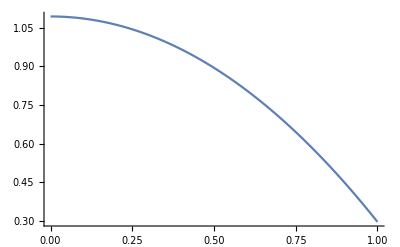
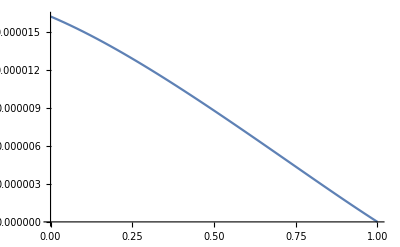
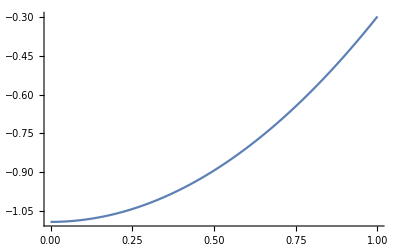
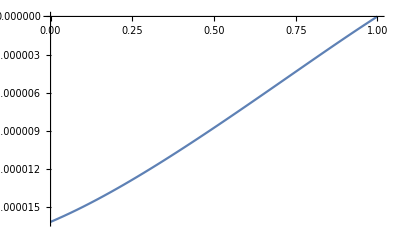
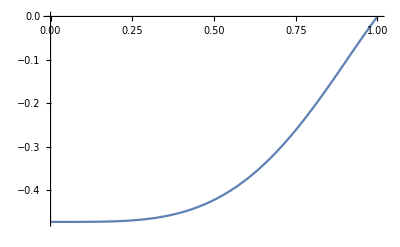
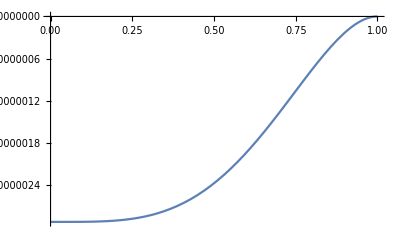
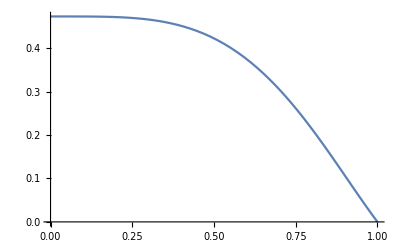
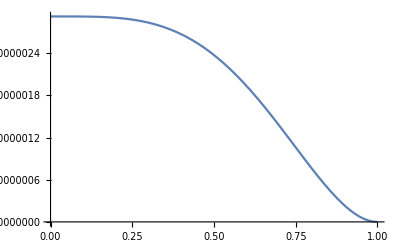
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
xxx=solSix[10^-5,0,-1,1,1,1];
{Plot[Re[xxx⟦1,#,2⟧],{z,0,1}],Plot[Im[xxx⟦1,#,2⟧],{z,0,1}]}&/@Range[6]
```

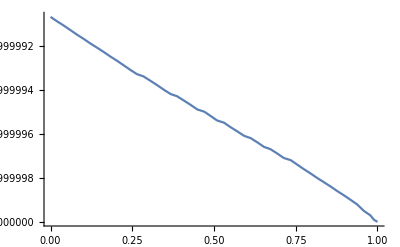
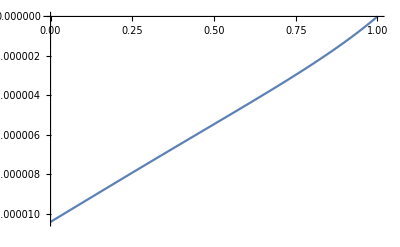
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
xxx=solSix[10^-5,0,1,1,1,-1];
{Plot[Re[xxx⟦1,#,2⟧],{z,0,1}],Plot[Im[xxx⟦1,#,2⟧],{z,0,1}]}&/@Range[6]
```

```mathematica
pureGauge1[ω_,k_,B_]={B,0,0,ⅈ ω,0,-ⅈ k}; 
pureGauge2[ω_,k_,B_]={0,B,-ⅈ ω,0,ⅈ k,0};

hIJ[ω_,k_]:=SetPrecision[Transpose[({{pureGauge1[ω,k,bSub]}, {pureGauge2[ω,k,bSub]}, {solSix[ω,k,-1,1,1,1]⟦1,;;,2⟧}, {solSix[ω,k,1,-1,1,1]⟦1,;;,2⟧}, {solSix[ω,k,1,1,-1,1]⟦1,;;,2⟧}, {solSix[ω,k,1,1,1,-1]⟦1,;;,2⟧}})] ,prec1]

hIJ0[ω_,k_]:=SetPrecision[hIJ[ω,k]/.z->zBdr,prec1]
hIJ0I[ω_,k_]:=SetPrecision[Inverse[hIJ0[ω,k]],prec1]
fQ[ω_,k_]:=SetPrecision[hIJ[ω,k].hIJ0I[ω,k],prec1]
fQp[ω_,k_]:=SetPrecision[D[fQ[ω,k],z] ,prec1]

first[ω_,k_]=SetPrecision[Table[firstTotal⟦i,j⟧,{i,6},{j,6}]/.{B->bSub,γ->γSub}//Simplify,prec1];
second[ω_,k_]=SetPrecision[Table[(secondBulk+secondCounter)⟦i,j⟧,{i,6},{j,6}]/.{B->bSub,γ->γSub}//Simplify,prec1];

green[ω_,k_]:=SetPrecision[-2(first[ω,k].fQp[ω,k]+second[ω,k]),prec1]
```

```mathematica
green[1/100,0]/.RNS/.{γ->γSub}/.μSub⟦1⟧/.z->zBdr
```

{{-1.456131952820134590082424294563766886+0.0007396930827575744297043550226692181 ⅈ,0.+0. ⅈ,-3.36414505313691225895505559996946229607775457964522210565478,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-1.456131952820134590082424294563766886+0.0007396930827575744297043550226692181 ⅈ,0,-3.36414505313691225895505559996946229607775457964522210565478,0.+0. ⅈ,0.+0. ⅈ},{-3.36414505304583242+8.71313×10^-12 ⅈ,0.+0. ⅈ,-5.829367984636389552,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-3.36414505304583242+8.71313×10^-12 ⅈ,0,-5.829367984636389552,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,-1.9430904003085365+0.0100007790226937 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,0.+0. ⅈ,-1.9430904003085365+0.0100007790226937 ⅈ}}

```mathematica
green[7,0]/.RNS/.{γ->γSub}/.μSub⟦1⟧/.z->zBdr
```

{{-89.6291344053019026649423123909864465523+76.950783387303854627249554531014977442 ⅈ,0.+0. ⅈ,-3.36414505313691225895505559996946229607775457964522210565478,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-89.6291344053019026649423123909864465523+76.950783387303854627249554531014977442 ⅈ,0,-3.36414505313691225895505559996946229607775457964522210565478,0.+0. ⅈ,0.+0. ⅈ},{-3.3641450523689122+8.088894×10^-10 ⅈ,0.+0. ⅈ,-5.829367984636389552,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-3.3641450523689122+8.088894×10^-10 ⅈ,0,-5.829367984636389552,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,-1102.5272439160690479+942.89855579130076944 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,0.+0. ⅈ,-1102.5272439160690479+942.89855579130076944 ⅈ}}

### ω grid

```mathematica
prec1=60;
ωgSize=50;
ωAxis=Table[L+ (1-Cos[(n π)/(2ωgSize-1)])(U-L),{n,0,2ωgSize-1}]⟦;;ωgSize⟧/.{L->10^-2,U->16π taap};
```

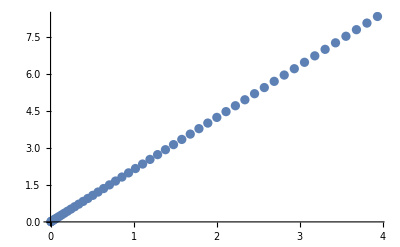

```mathematica
{ωAxis/(4π taap),ωAxis}//Transpose//ListPlot
```

```mathematica
ωAxis//Precision
```

∞

```mathematica
taap//Precision
```

∞

```mathematica
ωAxis⟦1⟧-ωAxis⟦2⟧//Precision
```

∞

```mathematica
ωAxis⟦-1⟧/(4π taap)//N
```

3.93661

### Computation

```mathematica
all=Table[SetPrecision[green[ωAxis⟦i⟧,0]/.RNS/.{γ->γSub}/.μSub⟦1⟧/.z->zBdr,prec1],{i,Length[ωAxis]}]
```

{{{-1.45613195282013459008242429456376688647830103179770164320371+0.00073969308275757442970435502266921813301743731685229077351 ⅈ,0.+0. ⅈ,-3.36414505313691225895505559996946229607775457964522210565478,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-1.45613195282013459008242429456376688647830103179770164320371+0.00073969308275757442970435502266921813301743731685229077351 ⅈ,0,-3.36414505313691225895505559996946229607775457964522210565478,0.+0. ⅈ,0.+0. ⅈ},{-3.36414505304583242023498013423076649807822288774259648479886+8.71313034134360084792480252357454228416815556618×10^-12 ⅈ,0.+0. ⅈ,-5.82936798463638955155574518480143175592280797687013338057027,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-3.36414505304583242023498013423076649807822288774259648479886+8.71313034134360084792480252357454228416815556618×10^-12 ⅈ,0,-5.82936798463638955155574518480143175592280797687013338057027,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,-1.94309040030853652612955367565656186673475271000765401963051+0.0100007790226936547507937279916852042869582656856378144461 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,0.+0. ⅈ,-1.94309040030853652612955367565656186673475271000765401963051+0.0100007790226936547507937279916852042869582656856378144461 ⅈ}},{{-1.45617175407963538468957402652240628588176665771907660172831+0.00105434625954479439211021728127844177787951381450997167431 ⅈ,0.+0. ⅈ,-3.36414505313691225895505559996946229607775457964522210565478,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-1.45617175407963538468957402652240628588176665771907660172831+0.00105434625954479439211021728127844177787951381450997167431 ⅈ,0,-3.36414505313691225895505559996946229607775457964522210565478,0.+0. ⅈ,0.+0. ⅈ},{-3.36414505304625376562471720160396611156814290783461057592063+1.23992587933803992950297638140950955312177871395×10^-11 ⅈ,0.+0. ⅈ,-5.82936798463638955155574518480143175592280797687013338057027,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-3.36414505304625376562471720160396611156814290783461057592063+1.23992587933803992950297638140950955312177871395×10^-11 ⅈ,0,-5.82936798463638955155574518480143175592280797687013338057027,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,-1.94305714369174626394334477358650493835788779142448507754326+0.01425396400751369490198707042885204361536530407852181763506 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,0.+0. ⅈ,-1.94305714369174626394334477358650493835788779142448507754326+0.01425396400751369490198707042885204361536530407852181763506 ⅈ}},{{-1.45637475177784045307159280355766300727740581869773958064545+0.00199917806703589520574032190182119294406008459206613548218 ⅈ,0.+0. ⅈ,-3.36414505313691225895505559996946229607775457964522210565478,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-1.45637475177784045307159280355766300727740581869500266958231+0.00199917806703589520574032190182119294406008459343459101374 ⅈ,0,-3.36414505313691225895505559996946229607775457964522210565478,0.+0. ⅈ,0.+0. ⅈ},{-3.3641450530483939642839191998177690958253929931656120476749+2.33149283326881887017542896574700537951058522748×10^-11 ⅈ,0.+0. ⅈ,-5.82936798463638955155574518480143175592280797687013338057027,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-3.3641450530483939642839191998177690958253929931656120476749+2.33149283326881887017542896574700537951058522748×10^-11 ⅈ,0,-5.82936798463638955155574518480143175592280797687013338057027,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,-1.94288761516581266620278824921641120377857596231765133568126+0.02701789239121678893101319161597857367278231027605704325789 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,0.+0. ⅈ,-1.94288761516581266620278824906494990997614169567859945114696+0.02701789239121678893101319191890116127765084355416081232648 ⅈ}},{{-1.45699088905676497323379173496502761590605900148816611353478+0.0035797603199543688513420309607693617239489282452124974473 ⅈ,0.+0. ⅈ,-3.36414505313691225895505559996946229607775457964522210565478,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-1.45699088905676497323379173496502761590605900148816611353478+0.0035797603199543688513420309607693617239489282452124974473 ⅈ,0,-3.36414505313691225895505559996946229607775457964522210565478,0.+0. ⅈ,0.+0. ⅈ},{-3.36414505305480031103120223102848854994404966495355913808085+4.069485452980736238413539531351422591737374695464×10^-11 ⅈ,0.+0. ⅈ,-5.82936798463638955155574518480143175592280797687013338057027,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-3.36414505305480031103120223102848854994404966495355913808085+4.069485452980736238413539531351422591737374695464×10^-11 ⅈ,0,-5.82936798463638955155574518480143175592280797687013338057027,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,-1.94237398239570635843379195877781371241870121571813229133241+0.0483271428483069588031027208734159776371522032080690206568 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,0.+0. ⅈ,-1.94237398239570635843379195877781371241870121571813229133241+0.0483271428483069588031027208734159776371522032080690206568 ⅈ}},{{-1.45843295354653160490979368964375930032382737447592795524479+0.00581524031014621495951721342976279091228248369144711680448 ⅈ,0.+0. ⅈ,-3.36414505313691225895505559996946229607775457964522210565478,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-1.45843295354653160490979368964375930032382737447592795524479+0.00581524031014621495951721342976279091228248369144711680448 ⅈ,0,-3.36414505313691225895505559996946229607775457964522210565478,0.+0. ⅈ,0.+0. ⅈ},{-3.36414505306927308508807877432756642939061616942269367612484+6.220061475300720719904535005789655101607284106574×10^-11 ⅈ,0.+0. ⅈ,-5.82936798463638955155574518480143175592280797687013338057027,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-3.36414505306927308508807877432756642939061616942269367612484+6.220061475300720719904535005789655101607284106574×10^-11 ⅈ,0,-5.82936798463638955155574518480143175592280797687013338057027,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,-1.94117725244077761938409402342210958520321762705684431188358+0.07831054167448613685937087241652681738627641393885297355082 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,0.+0. ⅈ,-1.94117725244077761938409402342210958520321762705684431188358+0.07831054167448613685937087241652681738627641393885297355082 ⅈ}},{{-1.46126746449847104776127004491618376423891987420512373089351+0.00875328334853064653354399032206033047475621807000439243734 ⅈ,0.+0. ⅈ,-3.36414505313691225895505559996946229607775457964522210565478,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-1.46126746449847104776127004491618376423891987420512373089351+0.00875328334853064653354399032206033047475621807000439243734 ⅈ,0,-3.36414505313691225895505559996946229607775457964522210565478,0.+0. ⅈ,0.+0. ⅈ},{-3.3641450530956405259744841517931677545917458511779443664988+8.264946852176688998786931611837777857083138163818×10^-11 ⅈ,0.+0. ⅈ,-5.82936798463638955155574518480143175592280797687013338057027,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-3.3641450530956405259744841517931677545917458511779443664988+8.264946852176688998786931611837777857083138163818×10^-11 ⅈ,0,-5.82936798463638955155574518480143175592280797687013338057027,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,-1.93884728516659370178619046392291573917474308033469113446423+0.1172967342586191757186176516401547345009771948106910063186 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,0.+0. ⅈ,-1.93884728516659370178619046392291573917474308033469113446423+0.1172967342586191757186176516401547345009771948106910063186 ⅈ}},{{-1.46619512068576047516385564445522532726836301461126880483803+0.01249169950206225453961571618087393211630831962842101511014 ⅈ,0.+0. ⅈ,-3.36414505313691225895505559996946229607775457964522210565478,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-1.46619512068576047516385564445522532726836301461126880483803+0.01249169950206225453961571618087393211630831962842101511014 ⅈ,0,-3.36414505313691225895505559996946229607775457964522210565478,0.+0. ⅈ,0.+0. ⅈ},{-3.36414505313520278957270396711540519426282643244071625908409+9.322567261874424339174880644985226993057530336939×10^-11 ⅈ,0.+0. ⅈ,-5.82936798463638955155574518480143175592280797687013338057027,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-3.36414505313520278957270396711540519426282643244071625908409+9.322567261874424339174880644985226993057530336939×10^-11 ⅈ,0,-5.82936798463638955155574518480143175592280797687013338057027,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,-1.93486817958841708387068119348062856420324737732776947118918+0.16595936405664380183586146441577918935773671220052535683898 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,0.+0. ⅈ,-1.93486817958841708387068119348062856420324737732776947118918+0.16595936405664380183586146441577918935773671220052535683898 ⅈ}},{{-1.47401416362284671503816220660461767126372171108961664005254+0.0172084128652916516546336944636286398806530615680508915843 ⅈ,0.+0. ⅈ,-3.36414505313691225895505559996946229607775457964522210565478,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-1.47401416362284671503816220660461767126372171108961664005254+0.0172084128652916516546336944636286398806530615680508915843 ⅈ,0,-3.36414505313691225895505559996946229607775457964522210565478,0.+0. ⅈ,0.+0. ⅈ},{-3.3641450531828802342986744435584405301812528766516890597546+8.271275637472097307290732127340542262539005002181×10^-11 ⅈ,0.+0. ⅈ,-5.82936798463638955155574518480143175592280797687013338057027,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-3.3641450531828802342986744435584405301812528766516890597546+8.271275637472097307290732127340542262539005002181×10^-11 ⅈ,0,-5.82936798463638955155574518480143175592280797687013338057027,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,-1.92874508110444518450197286963932272446346702001669409960727+0.22549894418057144382162055924518384720885663247328767160027 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,0.+0. ⅈ,-1.92874508110444518450197286963932272446346702001669409960727+0.22549894418057144382162055924518384720885663247328767160027 ⅈ}},{{-1.48555824409616837879267177997791381274872837951674922327183+0.02320331411942959277287042933630918342969776230408776729248 ⅈ,0.+0. ⅈ,-3.36414505313691225895505559996946229607775457964522210565478,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-1.48555824409616837879267177997791381274872837951674922327183+0.02320331411942959277287042933630918342969776230408776729248 ⅈ,0,-3.36414505313691225895505559996946229607775457964522210565478,0.+0. ⅈ,0.+0. ⅈ},{-3.36414505322372012564717157566751073639463923372046956668246+4.266793013727082235567713593402215813073273878442×10^-11 ⅈ,0.+0. ⅈ,-5.82936798463638955155574518480143175592280797687013338057027,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-3.36414505322372012564717157566751073639463923372046956668246+4.266793013727082235567713593402215813073273878442×10^-11 ⅈ,0,-5.82936798463638955155574518480143175592280797687013338057027,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,-1.92015071952853642519284836919944510365752484992864874621676+0.29785766636765274898208864525697083838669638397995921216821 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,0.+0. ⅈ,-1.92015071952853642519284836919944510365752484992864874621676+0.29785766636765274898208864525697083838669638397995921216821 ⅈ}},{{-1.50159860660024284586729241877493056453185452426454262075946+0.0309586535347265596965685136109477237630377406118015373224 ⅈ,0.+0. ⅈ,-3.36414505313691225895505559996946229607775457964522210565478,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-1.50159860660024284586729241877493056453185452426454262075946+0.0309586535347265596965685136109477237630377406118015373224 ⅈ,0,-3.36414505313691225895505559996946229607775457964522210565478,0.+0. ⅈ,0.+0. ⅈ},{-3.36414505323400607085249334027517276069181155963592816035557-2.28966093624206556892813544832082302382778200844×10^-11 ⅈ,0.+0. ⅈ,-5.82936798463638955155574518480143175592280797687013338057027,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-3.36414505323400607085249334027517276069181155963592816035557-2.28966093624206556892813544832082302382778200844×10^-11 ⅈ,0,-5.82936798463638955155574518480143175592280797687013338057027,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,-1.90915005105789476078270502677103182308209542711923615947167+0.38596345446353460807251227031392507181772175171781706290441 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,0.+0. ⅈ,-1.90915005105789476078270502677103182308209542711923615947167+0.38596345446353460807251227031392507181772175171781706290441 ⅈ}},{{-1.52269860035841521252152622724234975161348257380674759505261+0.04122963329298853559169471852311870813794318001660203798978 ⅈ,0.+0. ⅈ,-3.36414505313691225895505559996946229607775457964522210565478,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-1.52269860035841521252152622724234975161348257380674759505261+0.04122963329298853559169471852311870813794318001660203798978 ⅈ,0,-3.36414505313691225895505559996946229607775457964522210565478,0.+0. ⅈ,0.+0. ⅈ},{-3.36414505319285646553964161171241083597102846518480539789869-8.763716937684348991769325402897118450465017112927×10^-11 ⅈ,0.+0. ⅈ,-5.82936798463638955155574518480143175592280797687013338057027,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-3.36414505319285646553964161171241083597102846518480539789869-8.763716937684348991769325402897118450465017112927×10^-11 ⅈ,0,-5.82936798463638955155574518480143175592280797687013338057027,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,-1.89651892032060390401939714564874327071275283157643885834087+0.49400187712916641897211897532084975582340891346616205612174 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,0.+0. ⅈ,-1.89651892032060390401939714564874327071275283157643885834087+0.49400187712916641897211897532084975582340891346616205612174 ⅈ}},{{-1.54900684523675766523218415280730776424890480425447828804112+0.05518487830564069594029458287295898057369894750699737566746 ⅈ,0.+0. ⅈ,-3.36414505313691225895505559996946229607775457964522210565478,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-1.54900684523675766523218415280730776424890480425447828804112+0.05518487830564069594029458287295898057369894750699737566746 ⅈ,0,-3.36414505313691225895505559996946229607775457964522210565478,0.+0. ⅈ,0.+0. ⅈ},{-3.36414505310589858633557100876722045607080242209807477773986-1.051905576700776680734058194127886704669007540691×10^-10 ⅈ,0.+0. ⅈ,-5.82936798463638955155574518480143175592280797687013338057027,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-3.36414505310589858633557100876722045607080242209807477773986-1.051905576700776680734058194127886704669007540691×10^-10 ⅈ,0,-5.82936798463638955155574518480143175592280797687013338057027,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,-1.88416831579224652428636871659421126440166559348640641299855+0.62772080031772572303338238170580823308744681373339273540435 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,0.+0. ⅈ,-1.88416831579224652428636871659421126440166559348640641299855+0.62772080031772572303338238170580823308744681373339273540435 ⅈ}},{{-1.57997453150493023762608406436893658564454026359182153671566+0.07462944972061411441760918073420196769802403513604826701809 ⅈ,0.+0. ⅈ,-3.36414505313691225895505559996946229607775457964522210565478,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-1.57997453150493023762608406436893658564454026359318999224723+0.07462944972061411441760918073420196769802403513741672254966 ⅈ,0,-3.36414505313691225895505559996946229607775457964522210565478,0.+0. ⅈ,0.+0. ⅈ},{-3.36414505302658325817526701246062050714767946599126238575728-3.952957432144249117161916107746429902228420781574×10^-11 ⅈ,0.+0. ⅈ,-5.82936798463638955155574518480143175592280797687013338057027,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-3.36414505302658325817526701229653743886170901046562284417846-3.95295743214424908434530245055233879710051246581×10^-11 ⅈ,0,-5.82936798463638955155574518480143175592280797687013338057027,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,-1.87568158724944882616619172318649341807589626487961544099026+0.79478418339485067142018072234648520063797141679286760440615 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,0.+0. ⅈ,-1.87568158724944882616619172318649341807589626487961544099026+0.79478418339485067142018072234648520063797141679286760440615 ⅈ}},{{-1.61398438893577508123332080570670925585333023862844094131304+0.1023642140874940453551584837274916944593851115060712423086 ⅈ,0.+0. ⅈ,-3.36414505313691225895505559996946229607775457964522210565478,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-1.61398438893577508123332080570670925585333023862844094131304+0.1023642140874940453551584837274916944593851115060712423086 ⅈ,0,-3.36414505313691225895505559996946229607775457964522210565478,0.+0. ⅈ,0.+0. ⅈ},{-3.364145053038389989633346187925602965100061278866646415249+8.011279489016853384835592135337983400424554866759×10^-11 ⅈ,0.+0. ⅈ,-5.82936798463638955155574518480143175592280797687013338057027,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-3.364145053038389989633346187925602965100061278866646415249+8.011279489016853384835592135337983400424554866759×10^-11 ⅈ,0,-5.82936798463638955155574518480143175592280797687013338057027,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,-1.87697103254448285899743236685369257191741651153964599678392+1.0052079091443898784494524375452456908610027203522659881157 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,0.+0. ⅈ,-1.87697103254448285899743236685369257191741651153964599678392+1.0052079091443898784494524375452456908610027203522659881157 ⅈ}},{{-1.64788905349875129138779974527715243627439005989318925899711+0.14276955985957384733089508239571322613919481170179244070255 ⅈ,0.+0. ⅈ,-3.36414505313691225895505559996946229607775457964522210565478,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-1.64788905349875129138779974527715243627439005989318925899711+0.14276955985957384733089508239571322613919481170179244070255 ⅈ,0,-3.36414505313691225895505559996946229607775457964522210565478,0.+0. ⅈ,0.+0. ⅈ},{-3.36414505316830329876056275841863880025417119617856974087+1.359667249683592322561157785537322148808022422711×10^-10 ⅈ,0.+0. ⅈ,-5.82936798463638955155574518480143175592280797687013338057027,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-3.36414505316830329876056275841863880025417119617856974087+1.359667249683592322561157785537322148808022422711×10^-10 ⅈ,0,-5.82936798463638955155574518480143175592280797687013338057027,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,-1.89706533139053338003263403452598450450257220496617016278207+1.2719293211604486408671132762636013681106551831152123854807 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,0.+0. ⅈ,-1.89706533139053338003263403452598450450257220496617016278207+1.2719293211604486408671132762636013681106551831152123854807 ⅈ}},{{-1.67648706331197734800584499999733027901878974905219362126459+0.20275494096120326780878549282672945870391510860380322988114 ⅈ,0.+0. ⅈ,-3.36414505313691225895505559996946229607775457964522210565478,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-1.67648706331197734800584499999733027901878974905219362126459+0.20275494096120326780878549282672945870391510860380322988114 ⅈ,0,-3.36414505313691225895505559996946229607775457964522210565478,0.+0. ⅈ,0.+0. ⅈ},{-3.36414505329092582048970158568203627082980209991796096725969+2.15677383890635238257502203018252347908520743375×10^-11 ⅈ,0.+0. ⅈ,-5.82936798463638955155574518480143175592280797687013338057027,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-3.36414505329092582048970158568203627082980209991796096725969+2.15677383890635238257502203018252347908520743375×10^-11 ⅈ,0,-5.82936798463638955155574518480143175592280797687013338057027,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,-1.94905097740053680157801247924729573868699708683461645913892+1.6115788491712263180391609655617829116701960263256440935437 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,0.+0. ⅈ,-1.94905097740053680157801247924729573868699708683461645913892+1.6115788491712263180391609655617829116701960263256440935437 ⅈ}},{{-1.69204213802442879858921954529765594556322448821387788747789+0.29329305838529064183969690166421456267011047357089793491614 ⅈ,0.+0. ⅈ,-3.36414505313691225895505559996946229607775457964522210565478,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-1.69204213802442879858921954529765594556322448821387788747789+0.29329305838529064183969690166421456267011047357089793491614 ⅈ,0,-3.36414505313691225895505559996946229607775457964522210565478,0.+0. ⅈ,0.+0. ⅈ},{-3.36414505320757081696615907810931370306202111466128425697197-1.608571530086971060088335446676654311777310583584×10^-10 ⅈ,0.+0. ⅈ,-5.82936798463638955155574518480143175592280797687013338057027,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-3.36414505320757081696615907810931370306202111466128425697197-1.608571530086971060088335446676654311777310583584×10^-10 ⅈ,0,-5.82936798463638955155574518480143175592280797687013338057027,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,-2.05120664505372405759945453980146513346731901664211417980754+2.0455329275232776241858010233864177013292981725308555557979 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,0.+0. ⅈ,-2.05120664505372405759945453980146513346731901664211417980754+2.0455329275232776241858010233864177013292981725308555557979 ⅈ}},{{-1.68412972641337289900824756194653891680395310270549755199393+0.43184873275497427877101437501320190240666688451198127995845 ⅈ,0.+0. ⅈ,-3.36414505313691225895505559996946229607775457964522210565478,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-1.68412972641337289900824756194653891680395310270549755199393+0.43184873275497427877101437501320190240666688451198127995845 ⅈ,0,-3.36414505313691225895505559996946229607775457964522210565478,0.+0. ⅈ,0.+0. ⅈ},{-3.36414505297052616183231500960115352596373330882564172458066-1.128272391673646063641724192713272628730718010956×10^-10 ⅈ,0.+0. ⅈ,-5.82936798463638955155574518480143175592280797687013338057027,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-3.36414505297052616183231500960115352596373330882564172458066-1.128272391673646063641724192713272628730718010956×10^-10 ⅈ,0,-5.82936798463638955155574518480143175592280797687013338057027,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,-2.2283852422075477584680800634913708174773263663832163165163+2.60133150170156856031469087873441863804659379282068279448659 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,0.+0. ⅈ,-2.2283852422075477584680800634913708174773263663832163165163+2.60133150170156856031469087873441863804659379282068279448659 ⅈ}},{{-1.64047022366551742167574341689545766384155346562884605279568+0.6460539061415625638708821801397686125880297250343880078676 ⅈ,0.+0. ⅈ,-3.36414505313691225895505559996946229607775457964522210565478,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-1.64047022366551742167574341689545766384155346562884605279568+0.6460539061415625638708821801397686125880297250343880078676 ⅈ,0,-3.36414505313691225895505559996946229607775457964522210565478,0.+0. ⅈ,0.+0. ⅈ},{-3.36414505298996383546626672847702906385958738073489195617716+1.803944050681746514078379767394473230273700421061×10^-10 ⅈ,0.+0. ⅈ,-5.82936798463638955155574518480143175592280797687013338057027,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-3.36414505298996383546626672847702906385958738073489195617716+1.803944050681746514078379767394473230273700421061×10^-10 ⅈ,0,-5.82936798463638955155574518480143175592280797687013338057027,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,-2.5137116841967950201484158510019185008338845374763399244389+3.31454315465011328340579756201145760106585293879795134537602 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,0.+0. ⅈ,-2.5137116841967950201484158510019185008338845374763399244389+3.31454315465011328340579756201145760106585293879795134537602 ⅈ}},{{-1.55010483995267424513542621018216941848131077961023660240948+0.97875392020821363999743649167119746670349988882745347204094 ⅈ,0.+0. ⅈ,-3.36414505313691225895505559996946229607775457964522210565478,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-1.55010483995267424513542621018216941848131077961023660240948+0.97875392020821363999743649167119746670349988882745347204094 ⅈ,0,-3.36414505313691225895505559996946229607775457964522210565478,0.+0. ⅈ,0.+0. ⅈ},{-3.36414505334906592953737252010284355295244736206718930843218+1.699535062249720598783358791652823561190192250964×10^-10 ⅈ,0.+0. ⅈ,-5.82936798463638955155574518480143175592280797687013338057027,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-3.36414505334906592953737252010284355295244736206718930843218+1.699535062249720598783358791652823561190192250964×10^-10 ⅈ,0,-5.82936798463638955155574518480143175592280797687013338057027,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,-2.9506764299364129949882831905703192243409553947518198738914+4.23115934798722746984231489651269901070343321220851512745598 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,0.+0. ⅈ,-2.9506764299364129949882831905703192243409553947518198738914+4.23115934798722746984231489651269901070343321220851512745598 ⅈ}},{{-1.4112726652573351304696811606508422155928893023372322607803+1.49349552480042618093672610266644588538445653331139057666143 ⅈ,0.+0. ⅈ,-3.36414505313691225895505559996946229607775457964522210565478,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-1.4112726652573351304696811606508422155928893023372322607803+1.49349552480042618093672610266644588538445653331139057666143 ⅈ,0,-3.36414505313691225895505559996946229607775457964522210565478,0.+0. ⅈ,0.+0. ⅈ},{-3.36414505330934739498518461220548758821245186482439264597649-2.691239325452047528765172310809002406595567347472×10^-10 ⅈ,0.+0. ⅈ,-5.82936798463638955155574518480143175592280797687013338057027,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-3.36414505330934739498518461220548758821245186482439264597649-2.691239325452047528765172310809002406595567347472×10^-10 ⅈ,0,-5.82936798463638955155574518480143175592280797687013338057027,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,-3.5957199782707214691516961654639535395655692567020648552772+5.410596655403914199445004517084978299053529760363073514845 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,0.+0. ⅈ,-3.5957199782707214691516961654639535395655692567020648552772+5.410596655403914199445004517084978299053529760363073514845 ⅈ}},{{-1.2468645924609277170463436461094395987646514601636371572407+2.27663309297026628123745212715264494216201748439611895264238 ⅈ,0.+0. ⅈ,-3.36414505313691225895505559996946229607775457964522210565478,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-1.2468645924609277170463436461094395987646514601636371572407+2.27663309297026628123745212715264494216201748439611895264238 ⅈ,0,-3.36414505313691225895505559996946229607775457964522210565478,0.+0. ⅈ,0.+0. ⅈ},{-3.36414505278522815047557087831330419791133817042189069982522-1.346800443303631658573204310595103623906555745382×10^-10 ⅈ,0.+0. ⅈ,-5.82936798463638955155574518480143175592280797687013338057027,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-3.36414505278522815047557087831330419791133817042189069982522-1.346800443303631658573204310595103623906555745382×10^-10 ⅈ,0,-5.82936798463638955155574518480143175592280797687013338057027,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,-4.5214262447766571975180635928483584138206126649977721274065+6.92937747247386265450329505495002347508905637120900627284881 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,0.+0. ⅈ,-4.5214262447766571975180635928483584138206126649977721274065+6.92937747247386265450329505495002347508905637120900627284881 ⅈ}},{{-1.1274317808422491780940867933845413236251218839870501237647+3.42702013618948347111642984817168858337287676410956458510876 ⅈ,0.+0. ⅈ,-3.36414505313691225895505559996946229607775457964522210565478,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-1.1274317808422491780940867933845413236251218839870501237647+3.42702013618948347111642984817168858337287676410956458510876 ⅈ,0,-3.36414505313691225895505559996946229607775457964522210565478,0.+0. ⅈ,0.+0. ⅈ},{-3.36414505310902896492302975094154372470879274090220728901657+4.4106608413151376423611527545080072717653566025803×10^-10 ⅈ,0.+0. ⅈ,-5.82936798463638955155574518480143175592280797687013338057027,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-3.36414505310902896492302975094154372470879274090220728901657+4.4106608413151376423611527545080072717653566025803×10^-10 ⅈ,0,-5.82936798463638955155574518480143175592280797687013338057027,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,-5.8204736567937227550275496391544976163778483894561835507858+8.88553668855197374126003838161610028321014015306860962632729 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,0.+0. ⅈ,-5.8204736567937227550275496391544976163778483894561835507858+8.88553668855197374126003838161610028321014015306860962632729 ⅈ}},{{-1.1902454447386371640851768715260954777507764450646608746536+5.02114430202337394252306023196925699250070195707422266355573 ⅈ,0.+0. ⅈ,-3.36414505313691225895505559996946229607775457964522210565478,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-1.1902454447386371640851768715260954777507764450646608746536+5.02114430202337394252306023196925699250070195707422266355573 ⅈ,0,-3.36414505313691225895505559996946229607775457964522210565478,0.+0. ⅈ,0.+0. ⅈ},{-3.36414505362108088415465595379154651086008551615091650283107-1.688650234060371348684829767157748408012421167945×10^-10 ⅈ,0.+0. ⅈ,-5.82936798463638955155574518480143175592280797687013338057027,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-3.36414505362108088415465595379154651086008551615091650283107-1.688650234060371348684829767157748408012421167945×10^-10 ⅈ,0,-5.82936798463638955155574518480143175592280797687013338057027,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,-7.610526203195611428996333168340009115031120594331749554598+11.4037540577226855885714827391921508892101968390912617758171 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,0.+0. ⅈ,-7.610526203195611428996333168340009115031120594331749554598+11.4037540577226855885714827391921508892101968390912617758171 ⅈ}},{{-1.6248894726063944271817149144474265410179453769077499354997+7.05543378856699161126572247893335299285778085379081705537017 ⅈ,0.+0. ⅈ,-3.36414505313691225895505559996946229607775457964522210565478,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-1.6248894726063944271817149144474265410179453769077499354997+7.05543378856699161126572247893335299285778085379081705537017 ⅈ,0,-3.36414505313691225895505559996946229607775457964522210565478,0.+0. ⅈ,0.+0. ⅈ},{-3.36414505270829109506663055569514832902262391620471079431431-3.9632630170365051856779306395856582950197350301985×10^-10 ⅈ,0.+0. ⅈ,-5.82936798463638955155574518480143175592280797687013338057027,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-3.36414505270829109506663055569514832902262391620471079431431-3.9632630170365051856779306395856582950197350301985×10^-10 ⅈ,0,-5.82936798463638955155574518480143175592280797687013338057027,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,-10.040269562359727168143799710693111419956477954884148428086+14.6411318552338076668638427721322924041571965694390504084121 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,0.+0. ⅈ,-10.040269562359727168143799710693111419956477954884148428086+14.6411318552338076668638427721322924041571965694390504084121 ⅈ}},{{-2.6009523001033629582764862361777836816577480066122951220063+9.40748356073321756813499798003137134623937151798383180295229 ⅈ,0.+0. ⅈ,-3.36414505313691225895505559996946229607775457964522210565478,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-2.6009523001033629582764862361777836816577480066122951220063+9.40748356073321756813499798003137134623937151798383180295229 ⅈ,0,-3.36414505313691225895505559996946229607775457964522210565478,0.+0. ⅈ,0.+0. ⅈ},{-3.36414505302294262894014884295192656593221713941408107604453+6.3848424683018296687184467136906888988069164268119×10^-10 ⅈ,0.+0. ⅈ,-5.82936798463638955155574518480143175592280797687013338057027,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-3.36414505302294262894014884295192656593221713941408107604453+6.3848424683018296687184467136906888988069164268119×10^-10 ⅈ,0,-5.82936798463638955155574518480143175592280797687013338057027,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,-13.296790228505578764642054272138101394315344842843757159831+18.7934241132389400842297783496374759761733461542408652432401 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,0.+0. ⅈ,-13.296790228505578764642054272138101394315344842843757159831+18.7934241132389400842297783496374759761733461542408652432401 ⅈ}},{{-4.174967387396698648131252496351431187368553077748597450023+11.8766835136764207848798922882556295589220312965500804764807 ⅈ,0.+0. ⅈ,-3.36414505313691225895505559996946229607775457964522210565478,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-4.174967387396698648131252496351431187368553077748597450023+11.8766835136764207848798922882556295589220312965500804764807 ⅈ,0,-3.36414505313691225895505559996946229607775457964522210565478,0.+0. ⅈ,0.+0. ⅈ},{-3.36414505376553515679518950752915326027451648383494371176428-3.1320414481083003891098816917055087604256557662352×10^-10 ⅈ,0.+0. ⅈ,-5.82936798463638955155574518480143175592280797687013338057027,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-3.36414505376553515679518950752915326027451648383494371176428-3.1320414481083003891098816917055087604256557662352×10^-10 ⅈ,0,-5.82936798463638955155574518480143175592280797687013338057027,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,-17.614435135608857370684047601850058811299189798903360153898+24.1013884048103405232661850419411125029769565848575805545873 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,0.+0. ⅈ,-17.614435135608857370684047601850058811299189798903360153898+24.1013884048103405232661850419411125029769565848575805545873 ⅈ}},{{-6.2668271050179973268892133216208587974301149716196880794506+14.2921982782095634358051860654250694255446607258956376444078 ⅈ,0.+0. ⅈ,-3.36414505313691225895505559996946229607775457964522210565478,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-6.2668271050179973268892133216208587974301149716196880794506+14.2921982782095634358051860654250694255446607258956376444078 ⅈ,0,-3.36414505313691225895505559996946229607775457964522210565478,0.+0. ⅈ,0.+0. ⅈ},{-3.36414505245512079440940156165194729198036922994813075881576-2.9700581645892665191854876105389711456686719758674×10^-10 ⅈ,0.+0. ⅈ,-5.82936798463638955155574518480143175592280797687013338057027,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-3.36414505245512079440940156165194729198036922994813075881576-2.9700581645892665191854876105389711456686719758674×10^-10 ⅈ,0,-5.82936798463638955155574518480143175592280797687013338057027,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,-23.285155759339015496680290708647811564797277234386641085045+30.8568010332715008840090811245655653250369356229360952043744 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,0.+0. ⅈ,-23.285155759339015496680290708647811564797277234386641085045+30.8568010332715008840090811245655653250369356229360952043744 ⅈ}},{{-8.7300344804153648799068895527190388926027148507181918531048+16.5910180009444963367635428014971766676933517169132293148726 ⅈ,0.+0. ⅈ,-3.36414505313691225895505559996946229607775457964522210565478,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-8.7300344804153648799068895527190388926027148507181918531048+16.5910180009444963367635428014971766676933517169132293148726 ⅈ,0,-3.36414505313691225895505559996946229607775457964522210565478,0.+0. ⅈ,0.+0. ⅈ},{-3.36414505339411005860731661203276999285862692170565914091124+7.3058213616021085685280482436214332284865732771578×10^-10 ⅈ,0.+0. ⅈ,-5.82936798463638955155574518480143175592280797687013338057027,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-3.36414505339411005860731661203276999285862692170565914091124+7.3058213616021085685280482436214332284865732771578×10^-10 ⅈ,0,-5.82936798463638955155574518480143175592280797687013338057027,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,-30.670128752583826638956084699579049929061229128721588650663+39.407595375451020599074304958050470777737966499259229411975 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,0.+0. ⅈ,-30.670128752583826638956084699579049929061229128721588650663+39.407595375451020599074304958050470777737966499259229411975 ⅈ}},{{-11.439066313177460915105028213130812881015922965866314252404+18.8112901645507756445430219884637638476919912448809049345971 ⅈ,0.+0. ⅈ,-3.36414505313691225895505559996946229607775457964522210565478,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-11.439066313177460915105028213130812881015922965866314252404+18.8112901645507756445430219884637638476919912448809049345971 ⅈ,0,-3.36414505313691225895505559996946229607775457964522210565478,0.+0. ⅈ,0.+0. ⅈ},{-3.3641450534734807261931213921389743317598368052127085891384-7.238885933467253904239752611497227243312523525462×10^-10 ⅈ,0.+0. ⅈ,-5.82936798463638955155574518480143175592280797687013338057027,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-3.3641450534734807261931213921389743317598368052127085891384-7.238885933467253904239752611497227243312523525462×10^-10 ⅈ,0,-5.82936798463638955155574518480143175592280797687013338057027,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,-40.212177576101556022563972379388870284258746791977967008011+50.1616032727420659240618853873130405947577746327745412246307 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,0.+0. ⅈ,-40.212177576101556022563972379388870284258746791977967008011+50.1616032727420659240618853873130405947577746327745412246307 ⅈ}},{{-14.328817225919500621239088448760345214105875395174078624964+21.0401484341350104120568073891649079598771880514668440534402 ⅈ,0.+0. ⅈ,-3.36414505313691225895505559996946229607775457964522210565478,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-14.328817225919500621239088448760345214105875395174078624964+21.0401484341350104120568073891649079598771880514668440534402 ⅈ,0,-3.36414505313691225895505559996946229607775457964522210565478,0.+0. ⅈ,0.+0. ⅈ},{-3.36414505238584598155777877376064821663074591805741892121262+3.2473284816539830626585223803775167796561952268664×10^-10 ⅈ,0.+0. ⅈ,-5.82936798463638955155574518480143175592280797687013338057027,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-3.36414505238584598155777877376064821663074591805741892121262+3.2473284816539830626585223803775167796561952268664×10^-10 ⅈ,0,-5.82936798463638955155574518480143175592280797687013338057027,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,-52.448255774156794522273300031268476812733546227182016962604+63.5885418883305752728623119100368685265169783032138854997339 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,0.+0. ⅈ,-52.448255774156794522273300031268476812733546227182016962604+63.5885418883305752728623119100368685265169783032138854997339 ⅈ}},{{-17.389713309975376891057163146747388328961584425255510427549+23.3690844790889861984616126022974446601835614506276979472062 ⅈ,0.+0. ⅈ,-3.36414505313691225895505559996946229607775457964522210565478,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-17.389713309975376891057163146747388328961584425255510427549+23.3690844790889861984616126022974446601835614506276979472062 ⅈ,0,-3.36414505313691225895505559996946229607775457964522210565478,0.+0. ⅈ,0.+0. ⅈ},{-3.36414505394255182040910176480923782461141897443717210802738+2.261680418627079934991494020978310773167140783693×10^-10 ⅈ,0.+0. ⅈ,-5.82936798463638955155574518480143175592280797687013338057027,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-3.36414505394255182040910176480923782461141897443717210802738+2.261680418627079934991494020978310773167140783693×10^-10 ⅈ,0,-5.82936798463638955155574518480143175592280797687013338057027,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,-68.021082159490777044373122720515301900340845337136655261723+80.2201956886578900399811865480005910402669057278923791555469 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,0.+0. ⅈ,-68.021082159490777044373122720515301900340845337136655261723+80.2201956886578900399811865480005910402669057278923791555469 ⅈ}},{{-20.647533128317987521960867474437288693488001264161504537775+25.8727927197556963915248805808906434739877057388447504180731 ⅈ,0.+0. ⅈ,-3.36414505313691225895505559996946229607775457964522210565478,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-20.647533128317987521960867474437288693488001264161504537775+25.8727927197556963915248805808906434739877057388447504180731 ⅈ,0,-3.36414505313691225895505559996946229607775457964522210565478,0.+0. ⅈ,0.+0. ⅈ},{-3.3641450526120210724949415852624523496045876659648672006922-6.7531630477700287494659760508948368953247075405916×10^-10 ⅈ,0.+0. ⅈ,-5.82936798463638955155574518480143175592280797687013338057027,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-3.3641450526120210724949415852624523496045876659648672006922-6.7531630477700287494659760508948368953247075405916×10^-10 ⅈ,0,-5.82936798463638955155574518480143175592280797687013338057027,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,-87.689032209296969385125690668403670307862805671999075537298+100.649136044316012625330594661452848519109151443399433490528 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,0.+0. ⅈ,-87.689032209296969385125690668403670307862805671999075537298+100.649136044316012625330594661452848519109151443399433490528 ⅈ}},{{-24.145422800913113164501128751529194618431553719648940439794+28.6043356225452668135944179367896638894618645309557251000874 ⅈ,0.+0. ⅈ,-3.36414505313691225895505559996946229607775457964522210565478,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-24.145422800913113164501128751529194618431553719648940439794+28.6043356225452668135944179367896638894618645309557251000874 ⅈ,0,-3.36414505313691225895505559996946229607775457964522210565478,0.+0. ⅈ,0.+0. ⅈ},{-3.36414505319728058699877448815583569004374068513525577583251+8.7247817097596518298908009568661521051176929546223×10^-10 ⅈ,0.+0. ⅈ,-5.82936798463638955155574518480143175592280797687013338057027,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-3.36414505319728058699877448815583569004374068513525577583251+8.7247817097596518298908009568661521051176929546223×10^-10 ⅈ,0,-5.82936798463638955155574518480143175592280797687013338057027,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,-112.33363484519285999772006873092874980068240812468044909772+125.526680346996269591674362540580231343405857301172225300168 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,0.+0. ⅈ,-112.33363484519285999772006873092874980068240812468044909772+125.526680346996269591674362540580231343405857301172225300168 ⅈ}},{{-27.932156578142078428420362030201113633959615931666749245151+31.5973195781140615499331531890052631843568095074599717475022 ⅈ,0.+0. ⅈ,-3.36414505313691225895505559996946229607775457964522210565478,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-27.932156578142078428420362030201113633959615931666749245151+31.5973195781140615499331531890052631843568095074599717475022 ⅈ,0,-3.36414505313691225895505559996946229607775457964522210565478,0.+0. ⅈ,0.+0. ⅈ},{-3.3641450535491914201587624368348248172280537798309286382642-7.9411862018516703479472305260543831155876947670846×10^-10 ⅈ,0.+0. ⅈ,-5.82936798463638955155574518480143175592280797687013338057027,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-3.3641450535491914201587624368348248172280537798309286382642-7.9411862018516703479472305260543831155876947670846×10^-10 ⅈ,0,-5.82936798463638955155574518480143175592280797687013338057027,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,-142.96446075494944205319948263192975037503064003456700438791+155.56097759596401487832632481400872304588702325800378227505 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,0.+0. ⅈ,-142.96446075494944205319948263192975037503064003456700438791+155.56097759596401487832632481400872304588702325800378227505 ⅈ}},{{-32.055369184599321210174057482849841928026879827506890984056+34.8699829886597227167319900388303142255557559324942172680426 ⅈ,0.+0. ⅈ,-3.36414505313691225895505559996946229607775457964522210565478,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-32.055369184599321210174057482849841928026879827506890984056+34.8699829886597227167319900388303142255557559324942172680426 ⅈ,0,-3.36414505313691225895505559996946229607775457964522210565478,0.+0. ⅈ,0.+0. ⅈ},{-3.36414505237393754428314782572492768980070525222932456034519+5.0661674540360708649554308582399476453361308707357×10^-10 ⅈ,0.+0. ⅈ,-5.82936798463638955155574518480143175592280797687013338057027,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-3.36414505237393754428314782572492768980070525222932456034519+5.0661674540360708649554308582399476453361308707357×10^-10 ⅈ,0,-5.82936798463638955155574518480143175592280797687013338057027,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,-180.72168844639636964590507332536315657702563201060925969152+191.516020084512042288630027319650835913766661460830553189924 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,0.+0. ⅈ,-180.72168844639636964590507332536315657702563201060925969152+191.516020084512042288630027319650835913766661460830553189924 ⅈ}},{{-36.557889505012758392163117655105649995668578740977029303274+38.4293188280139172361217974571468818892915832292762397125719 ⅈ,0.+0. ⅈ,-3.36414505313691225895505559996946229607775457964522210565478,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-36.557889505012758392163117655105649995668578740977029303274+38.4293188280139172361217974571468818892915832292762397125719 ⅈ,0,-3.36414505313691225895505559996946229607775457964522210565478,0.+0. ⅈ,0.+0. ⅈ},{-3.36414505406775270290013184880415971902590568765899540180919-1.12830390047649578614789721090616181731582697706×10^-10 ⅈ,0.+0. ⅈ,-5.82936798463638955155574518480143175592280797687013338057027,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-3.36414505406775270290013184880415971902590568765899540180919-1.12830390047649578614789721090616181731582697706×10^-10 ⅈ,0,-5.82936798463638955155574518480143175592280797687013338057027,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,-226.87702330746140431273853250543905975126038255882865890718+234.212023142339292625066826303055007509213959410574763938748 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,0.+0. ⅈ,-226.87702330746140431273853250543905975126038255882865890718+234.212023142339292625066826303055007509213959410574763938748 ⅈ}},{{-41.475960854970549953151933084921798098665652087035812525093+42.27474409892601160258853357759653165692530071317299730466 ⅈ,0.+0. ⅈ,-3.36414505313691225895505559996946229607775457964522210565478,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-41.475960854970549953151933084921798098665652087035812525093+42.27474409892601160258853357759653165692530071317299730466 ⅈ,0,-3.36414505313691225895505559996946229607775457964522210565478,0.+0. ⅈ,0.+0. ⅈ},{-3.36414505222184301196691415310997763605448925018513901558787-2.899846318799669421075439436848249755302451332456×10^-10 ⅈ,0.+0. ⅈ,-5.82936798463638955155574518480143175592280797687013338057027,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-3.36414505222184301196691415310997763605448925018513901558787-2.899846318799669421075439436848249755302451332456×10^-10 ⅈ,0,-5.82936798463638955155574518480143175592280797687013338057027,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,-282.83378222930966261494980678394050811485502261141664645354+284.527099969832186289337406753563538043537383085850495144722 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,0.+0. ⅈ,-282.83378222930966261494980678394050811485502261141664645354+284.527099969832186289337406753563538043537383085850495144722 ⅈ}},{{-46.8387049241860575805273371727639134319715679830891836766442+46.40120971751485144788873228914712450271000857872976184594 ⅈ,0.+0. ⅈ,-3.36414505313691225895505559996946229607775457964522210565478,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-46.8387049241860575805273371727639134319715679830919205877074+46.40120971751485144788873228914712450271000857872976184594 ⅈ,0,-3.36414505313691225895505559996946229607775457964522210565478,0.+0. ⅈ,0.+0. ⅈ},{-3.36414505388903729827342157709695209276078109940743394133678+6.320208215034876093197954827685688914697646756391×10^-10 ⅈ,0.+0. ⅈ,-5.82936798463638955155574518480143175592280797687013338057027,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-3.36414505388903729827342157709695209276078109940743394133678+6.320208215034876093197954827685688914697646756391×10^-10 ⅈ,0,-5.82936798463638955155574518480143175592280797687013338057027,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,-350.126800542149670921858274730418627980732651549036771321255+343.39966281658637288480790230474359312154010986505459773754 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,0.+0. ⅈ,-350.126800542149670921858274730418627980732651549036771321255+343.39966281658637288480790230474359312154010986505459773754 ⅈ}},{{-52.66845425534708844257523251164134806930224143544826984932+50.80168277383973358738240656961349258108855519579982824404 ⅈ,0.+0. ⅈ,-3.36414505313691225895505559996946229607775457964522210565478,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-52.66845425534708844257523251164134806930224143544826984932+50.80168277383973358738240656961349258108855519579982824404 ⅈ,0,-3.36414505313691225895505559996946229607775457964522210565478,0.+0. ⅈ,0.+0. ⅈ},{-3.36414505264374997867095339022929713773689223220539519509931-8.7562722762064909878630732338953216560463053887847×10^-10 ⅈ,0.+0. ⅈ,-5.82936798463638955155574518480143175592280797687013338057027,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-3.36414505264374997867095339022929713773689223220539519509931-8.7562722762064909878630732338953216560463053887847×10^-10 ⅈ,0,-5.82936798463638955155574518480143175592280797687013338057027,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,-430.422442177653079639455959149074175631432473491465008847215+411.83066471146493522712339214871390093837411981844611602588 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,0.+0. ⅈ,-430.422442177653079639455959149074175631432473491465008847215+411.83066471146493522712339214871390093837411981844611602588 ⅈ}},{{-58.9816505052372555311241217514162302438443492912826002150001+55.468936969251835565267637123512914298570871539014906142657 ⅈ,0.+0. ⅈ,-3.36414505313691225895505559996946229607775457964522210565478,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-58.9816505052372555311241217514162302438443492912826002150001+55.468936969251835565267637123512914298570871539014906142657 ⅈ,0,-3.36414505313691225895505559996946229607775457964522210565478,0.+0. ⅈ,0.+0. ⅈ},{-3.36414505332499077662484142975678808764136610378739703202527+1.0100192139037405871922268116217466132644606192567×10^-9 ⅈ,0.+0. ⅈ,-5.82936798463638955155574518480143175592280797687013338057027,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-3.36414505332499077662484142975678808764136610378739703202527+1.0100192139037405871922268116217466132644606192567×10^-9 ⅈ,0,-5.82936798463638955155574518480143175592280797687013338057027,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,-525.518543261796638586564604435135641454639160132941645611065+490.88473520052330038001401688362189639930722771747804663613 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,0.+0. ⅈ,-525.518543261796638586564604435135641454639160132941645611065+490.88473520052330038001401688362189639930722771747804663613 ⅈ}},{{-65.7900176496299087178356746336872980845895806108582643411033+60.396639023180095744380257171121379311733731921518226372575 ⅈ,0.+0. ⅈ,-3.36414505313691225895505559996946229607775457964522210565478,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-65.7900176496299087178356746336872980845895806108582643411033+60.396639023180095744380257171121379311733731921518226372575 ⅈ,0,-3.36414505313691225895505559996946229607775457964522210565478,0.+0. ⅈ,0.+0. ⅈ},{-3.36414505325977266197823686033406066902677304292640099014217-1.0423818399339332710234556184956871013605814299194×10^-9 ⅈ,0.+0. ⅈ,-5.82936798463638955155574518480143175592280797687013338057027,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-3.36414505325977266197823686033406066902677304292640099014217-1.0423818399339332710234556184956871013605814299194×10^-9 ⅈ,0,-5.82936798463638955155574518480143175592280797687013338057027,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,-637.3437417443125424251778959371651654262417507613609226301+581.68943704613122224038146742381656302742351704166445564188 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,0.+0. ⅈ,-637.3437417443125424251778959371651654262417507613609226301+581.68943704613122224038146742381656302742351704166445564188 ⅈ}},{{-73.1017491056158777147927912671859954200334209703247160941167+65.579801793671127969324345593075055823037664977748349414332 ⅈ,0.+0. ⅈ,-3.36414505313691225895505559996946229607775457964522210565478,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-73.1017491056158777147927912671859954200334209703247160941167+65.579801793671127969324345593075055823037664977748349414332 ⅈ,0,-3.36414505313691225895505559996946229607775457964522210565478,0.+0. ⅈ,0.+0. ⅈ},{-3.36414505272536608036832280405761490612107075642043879041415+9.8935639628301027655522227087806212633064111786757×10^-10 ⅈ,0.+0. ⅈ,-5.82936798463638955155574518480143175592280797687013338057027,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-3.36414505272536608036832280405761490612107075642043879041415+9.8935639628301027655522227087806212633064111786757×10^-10 ⅈ,0,-5.82936798463638955155574518480143175592280797687013338057027,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,-767.955436145944291483497177412988576261992524905997483698761+685.43218631730923975610182689881608191847189449465711070207 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,0.+0. ⅈ,-767.955436145944291483497177412988576261992524905997483698761+685.43218631730923975610182689881608191847189449465711070207 ⅈ}},{{-80.9225153522837407045147136829158255386998819593546684219505+71.014747282710317865493606125943768900697893381424126668627 ⅈ,0.+0. ⅈ,-3.36414505313691225895505559996946229607775457964522210565478,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-80.9225153522837407045147136829158255386998819593546684219505+71.014747282710317865493606125943768900697893381424126668627 ⅈ,0,-3.36414505313691225895505559996946229607775457964522210565478,0.+0. ⅈ,0.+0. ⅈ},{-3.36414505379796232744977350415509485407052690954295289492426-8.7065588606169409168627202087300566932541370096521×10^-10 ⅈ,0.+0. ⅈ,-5.82936798463638955155574518480143175592280797687013338057027,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-3.36414505379796232744977350415509485407052690954295289492426-8.7065588606169409168627202087300566932541370096521×10^-10 ⅈ,0,-5.82936798463638955155574518480143175592280797687013338057027,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,-919.535597268183298607536715999715132626612928547760308700329+803.35472343519276247640965835077229965222254245457470206264 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,0.+0. ⅈ,-919.535597268183298607536715999715132626612928547760308700329+803.35472343519276247640965835077229965222254245457470206264 ⅈ}},{{-89.2561874335268180994082674920669139561471771516171949605108+76.698757149564559924065229326143581318698979418735194342588 ⅈ,0.+0. ⅈ,-3.36414505313691225895505559996946229607775457964522210565478,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-89.2561874335268180994082674920669139561471771516171949605108+76.698757149564559924065229326143581318698979418735194342588 ⅈ,0,-3.36414505313691225895505559996946229607775457964522210565478,0.+0. ⅈ,0.+0. ⅈ},{-3.36414505227382441632836284976000757829965949310560373568951+7.0509670897230067722600904018678589349633934867806×10^-10 ⅈ,0.+0. ⅈ,-5.82936798463638955155574518480143175592280797687013338057027,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-3.36414505227382441632836284976000757829965949310560373568951+7.0509670897230067722600904018678589349633934867806×10^-10 ⅈ,0,-5.82936798463638955155574518480143175592280797687013338057027,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,-1094.38379095095846651896976324683915446231337445806509802576+936.74530756274316709188074101118055810142242867008557341731 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,0.+0. ⅈ,-1094.38379095095846651896976324683915446231337445806509802576+936.74530756274316709188074101118055810142242867008557341731 ⅈ}},{{-98.1052559849403808807492398024190508724771337869005075309312+82.629580718347683935990951412289825483602677498283802774103 ⅈ,0.+0. ⅈ,-3.36414505313691225895505559996946229607775457964522210565478,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-98.1052559849403808807492398024190508724771337869005075309312+82.629580718347683935990951412289825483602677498283802774103 ⅈ,0,-3.36414505313691225895505559996946229607775457964522210565478,0.+0. ⅈ,0.+0. ⅈ},{-3.36414505415209874326293015697628677898476709836286964710322-5.0863169679061309781356610103093402984667631937243×10^-10 ⅈ,0.+0. ⅈ,-5.82936798463638955155574518480143175592280797687013338057027,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-3.36414505415209874326293015697628677898476709836286964710322-5.0863169679061309781356610103093402984667631937243×10^-10 ⅈ,0,-5.82936798463638955155574518480143175592280797687013338057027,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,-1294.90699153209446010820086231749877646966620796814697409369+1086.9289838784311700250484632293209530919402644098703428037 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,0.+0. ⅈ,-1294.90699153209446010820086231749877646966620796814697409369+1086.9289838784311700250484632293209530919402644098703428037 ⅈ}},{{-107.470986183283401462552394230395854480270273334676776611738+88.80493325819117401672885334645020582431345162289923730512 ⅈ,0.+0. ⅈ,-3.36414505313691225895505559996946229607775457964522210565478,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-107.470986183283401462552394230395854480270273334676776611738+88.80493325819117401672885334645020582431345162289923730512 ⅈ,0,-3.36414505313691225895505559996946229607775457964522210565478,0.+0. ⅈ,0.+0. ⅈ},{-3.36414505201870980897502907018803230930630951176388645541826+2.9377249357994598120180343375808412193216654154093×10^-10 ⅈ,0.+0. ⅈ,-5.82936798463638955155574518480143175592280797687013338057027,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-3.36414505201870980897502907018803230930630951176388645541826+2.9377249357994598120180343375808412193216654154093×10^-10 ⅈ,0,-5.82936798463638955155574518480143175592280797687013338057027,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,-1523.60600749733797486238212880736995620704584894912725053298+1255.2563371168997791156374066675161138539246608806462010121 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,0.+0. ⅈ,-1523.60600749733797486238212880736995620704584894912725053298+1255.2563371168997791156374066675161138539246608806462010121 ⅈ}},{{-117.353380410575749177715355943083097275122391569583642410916+95.222068468212962708451962260180048540644591965873964631722 ⅈ,0.+0. ⅈ,-3.36414505313691225895505559996946229607775457964522210565478,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-117.353380410575749177715355943083097275122391569583642410916+95.222068468212962708451962260180048540644591965873964631722 ⅈ,0,-3.36414505313691225895505559996946229607775457964522210565478,0.+0. ⅈ,0.+0. ⅈ},{-3.36414505431134047973371747514737940927321942959025958229391-6.985008260078725675160572032984358911782932655826×10^-11 ⅈ,0.+0. ⅈ,-5.82936798463638955155574518480143175592280797687013338057027,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-3.36414505431134047973371747514737940927321942959025958229391-6.985008260078725675160572032984358911782932655826×10^-11 ⅈ,0,-5.82936798463638955155574518480143175592280797687013338057027,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,-1783.05855261504275425381626969319655413779893011266358899061+1443.0911185325029185580408713545508449326484958365943145602 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,0.+0. ⅈ,-1783.05855261504275425381626969319655413779893011266358899061+1443.0911185325029185580408713545508449326484958365943145602 ⅈ}},{{-127.751026264021489025816173710065051990012832997283376948423+101.87746330843841482821379746230381560674792817012376850435 ⅈ,0.+0. ⅈ,-3.36414505313691225895505559996946229607775457964522210565478,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-127.751026264021489025816173710065051990012832997283376948423+101.87746330843841482821379746230381560674792817012376850435 ⅈ,0,-3.36414505313691225895505559996946229607775457964522210565478,0.+0. ⅈ,0.+0. ⅈ},{-3.36414505195061561749857664464275401721307576168815698172687-1.562866582044839626313992243658140958842471621854×10^-10 ⅈ,0.+0. ⅈ,-5.82936798463638955155574518480143175592280797687013338057027,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-3.36414505195061561749857664464275401721307576168815698172687-1.562866582044839626313992243658140958842471621854×10^-10 ⅈ,0,-5.82936798463638955155574518480143175592280797687013338057027,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,-2075.89915072210528888341607335652596128358460668139335702359+1651.7970534585985517605893243789600032703957193574032858742 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,0.+0. ⅈ,-2075.89915072210528888341607335652596128358460668139335702359+1651.7970534585985517605893243789600032703957193574032858742 ⅈ}},{{-138.660896786024419923744836450581305334785852141638689663307+108.76661895842374293635503453954053724015354115840118464476 ⅈ,0.+0. ⅈ,-3.36414505313691225895505559996946229607775457964522210565478,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-138.660896786024419923744836450581305334785852141638689663307+108.76661895842374293635503453954053724015354115840118464476 ⅈ,0,-3.36414505313691225895505559996946229607775457964522210565478,0.+0. ⅈ,0.+0. ⅈ},{-3.36414505429251115071898037104915073136900245991947754238549+3.7938242489628013239890710558973806515395291259068×10^-10 ⅈ,0.+0. ⅈ,-5.82936798463638955155574518480143175592280797687013338057027,0,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-3.36414505429251115071898037104915073136900245991947754238549+3.7938242489628013239890710558973806515395291259068×10^-10 ⅈ,0,-5.82936798463638955155574518480143175592280797687013338057027,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,-2404.79615477721609567078564675774164327897918011232698495307+1882.7240392288576460096210688346288663541106399108626462055 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0,0,0.+0. ⅈ,-2404.79615477721609567078564675774164327897918011232698495307+1882.7240392288576460096210688346288663541106399108626462055 ⅈ}}}

```mathematica
all//Dimensions
```

{50,6,6}

```mathematica
toSave={{2/(√3),mutilde,bSub,taap,entropy,n0,p0,kSub},all};
```

```mathematica
SetDirectory[NotebookDirectory[]<>"f_data"];
Save["corrγSUSYμT"<>ToString[mutilde]<>"B"<>ToString[100bSub]<>"d100",toSave]
```